## Analyze My Week Activities

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\USERS\Guokr\Documents\GitHub\WhyMathematica\Web\WebExtraction\UserAnswersGuokr

Memory Management

```mathematica
(*
ClearMemory:=Module[{},Unprotect[In,Out];Clear[In,Out];Protect[In,Out];ClearSystemCache[];];
*)
```

### Variables

长老：userIDNumber=”0247833600”
橡胶：userIDNumber=”1351044112”
tangcubibi   1392375419
fengfeixue0219: 1907123879
子夜：1900615460
时见疏星：1769480175
wugui: 0618908094
cast  1834626891
Ent: 2063560525
Obliviou_s 0207550923
C.CristataX    1348935424

```mathematica
userIDNumber="1348935424"
urlAnswers="http://www.guokr.com/i/"<>ToString[userIDNumber]<>"/answers"
```

1348935424

http://www.guokr.com/i/1348935424/answers

### Data Extraction

```mathematica
rawData0=Import[urlAnswers,"XMLObject",CharacterEncoding->"UTF-8"];
```

#### Basic Infomation

Get the ID by this element
XMLElement[span,{itemprop→name},{时见疏星}]

```mathematica
userID=Cases[rawData0,XMLElement["span",{"itemprop"->"name"},{id_}]:>id,Infinity][[1]]
```

C.CristataX

Get user image by 
XMLElement[img,{itemprop→image,alt→时见疏星,width→160,height→160,src→http://img1.guokr.com/thumbnail/TcCEQCVVXmDne6eXJv4nOu5LSGuaqh_kjG6U_NfdSi-gAAAAoAAAAEpQ_160x160.jpg},{}]

```mathematica
userIMG=Import[Cases[rawData0,XMLElement["img",{"itemprop"->"image","alt"->id_,"width"->"160","height"->"160","src"->imgurl_},{}]:>{imgurl,id},Infinity][[1]][[1]]]
```

-Graphics-

Get the number of answers by
XMLElement[span,{class→side-title},{
                        ,XMLElement[span,{class→gicon-answer-actived},{}],回答：
                        ,XMLElement[span,{class→side-title-more},{113条}],
                    }]

```mathematica
numberAnswers=Cases[rawData0,XMLElement["span",{"class"->"side-title"},{"\n                        ",XMLElement["span",{"class"->"gicon-answer-actived"},{}],"回答：\n                        ",XMLElement["span",{"class"->"side-title-more"},{ansNumber_}],"\n                    "}]:>ansNumber,Infinity][[1]]
```

152条

how many pages can be shown by this element
XMLElement[a,{shape→rect,href→/i/1769480175/answers/?page=12},{末页}],

#### All Answers Pages

```mathematica
pages=ToExpression[StringSplit[Cases[rawData0,XMLElement["a",{"shape"->"rect","href"->href_},{"末页"}]:>href,Infinity],"="][[1]][[2]]]
```

16

Generate All URLs of answers pages

```mathematica
urlAnswersList=ParallelTable[urlAnswers<>"/?page="<>ToString[i],{i,1,pages}];
```

#### All Answers URL

Extract all urls of answers

```mathematica
answerURLList=Flatten[ParallelTable[Cases[Import[urlAnswersList[[i]],"XMLObject",CharacterEncoding->"UTF-8"],XMLElement["a",{"shape"->"rect","target"->"_blank","href"->url_},{"查看全文"}]:>url,Infinity],{i,1,pages}]];
```

```mathematica
answerURLListT=StringTrim[answerURLList,"redirect/"];
```

```mathematica
answerURLListLen=Length[answerURLListT]
```

148

I would like to comment this line out because this takes too much memory

```mathematica
answerRawData=ParallelTable[Import[answerURLListT[[i]],"XMLObject",CharacterEncoding->"UTF-8"],{i,1,answerURLListLen}];
```

```mathematica
answerExpRawData=Export[StringJoin["Data\\AnsRawData","USR",ToString[userID],"-",DateString[{"Day","-","Month","-","YearShort"}],".xml"],answerRawData,"XML"]
```

Export::nodir: Directory "C:\\Users\\Guokr\\Documents\\Data\\" does not exist.

Export::noopen: Cannot open "Data\\AnsRawDataUSRC.CristataX-18-07-13.xml".

$Failed

Remove answerRawData so that it won’t stay in memory.

```mathematica
Remove[answerExpRawData]
```

```mathematica
answerDataSourceDate=ParallelTable[StringSplit[Cases[answerRawData[[i]],XMLElement["p",{"class"->"answer-date"},{date_}]:>date,Infinity][[1]]][[1]],{i,1,answerURLListLen}];
```

```mathematica
answerDataSourceQTitle=ParallelTable[Cases[answerRawData[[i]],XMLElement["h1",{"id"->"articleTitle"},{title_}]:>title,Infinity],{i,1,answerURLListLen}];
```

```mathematica
answerDataSourceUp=ParallelTable[Cases[answerRawData[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]},Infinity][[1]],{i,1,answerURLListLen}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
answerSupLen=Total[Table[ToExpression[answerDataSourceUp[[i]][[2]]],{i,1,answerURLListLen}]]
```

148

```mathematica
answerDataSourceDown=Table[Cases[answerRawData[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-dw","href"->"javascript:void 0;","data-operation"->"oppose","data-id"->labela_,"title"->"反对(-1)"},{labelb_}]:>{labela,labelb},Infinity][[1]],{i,1,answerURLListLen}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
answerDownLen=Total[Table[ToExpression[answerDataSourceDown[[i]][[2]]],{i,1,answerURLListLen}]]
```

148

Average Vote-ups of my answers

```mathematica
answerSupAvg=N[answerSupLen/answerURLListLen]
```

1.

Remove answerRawData so that it won’t stay in memory.

```mathematica
Remove[answerRawData]
```

```mathematica
answerGridTable=Prepend[
Prepend[Prepend[
Sort[Table[{answerDataSourceUp[[i]][[1]],answerDataSourceDate[[i]],ToExpression[answerDataSourceUp[[i]][[2]]],answerDataSourceDown[[i]][[2]],Hyperlink[answerDataSourceQTitle[[i]][[1]],answerURLList[[i]]]},{i,1,answerURLListLen}],#1[[3]]>#2[[3]]&]
,{"Answer ID","Post Date","Vote-up","Vote-down","Title"}],{"总回答数："<>ToString[answerURLListLen]<>"； "<>"总支持数："<>ToString[answerSupLen]<>"； "<>"总反对数："<>ToString[answerDownLen]<>"；"<>"平均支持数"<>ToString[answerSupAvg]<>"；",SpanFromLeft}]
,{"用户："<>ToString[userID]<>":"<>"回答问题"<>"("<>DateString[{"Day","-","Month","-","YearShort"}]<>")",SpanFromLeft}];
```

The table below is not dynamicly need for the computing

```mathematica
answerTable=Grid[answerGridTable,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}];
```

```mathematica
(*
answerTable=Dynamic[Grid[answerGridTable,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}]]//Quiet
*)
```

```mathematica
answerGridTableLink=Prepend[
Prepend[Prepend[
Sort[Table[{answerDataSourceDate[[i]],Hyperlink[answerDataSourceQTitle[[i]][[1]],answerURLList[[i]]],answerURLList[[i]]},{i,1,answerURLListLen}],#1[[3]]>#2[[3]]&]
,{"Post Date","Title","Link"}],{"总回答数："<>ToString[answerURLListLen]<>"； "<>"总支持数："<>ToString[answerSupLen]<>"； "<>"总反对数："<>ToString[answerDownLen]<>"；"<>"平均支持数"<>ToString[answerSupAvg]<>"；",SpanFromLeft}]
,{"用户："<>ToString[userID]<>":"<>"回答问题"<>"("<>DateString[{"Day","-","Month","-","YearShort"}]<>")",SpanFromLeft}];
```

```mathematica
answerTableLink=Grid[answerGridTableLink,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}];
```

```mathematica
%
```

用户：C.CristataX:回答问题(18-07-13) |  | 
总回答数：148； 总支持数：148； 总反对数：148；平均支持数1.； |  | 
Post Date | Title | Link
2013-07-16 |  | http://www.guokr.com/answer/524511/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524502/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524500/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524484/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524481/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524480/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524319/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524317/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524266/redirect/
2013-07-16 |  | http://www.guokr.com/answer/524264/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523953/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523946/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523941/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523940/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523672/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523670/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523669/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523477/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523472/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523454/redirect/
2013-07-15 |  | http://www.guokr.com/answer/523451/redirect/
2013-07-14 |  | http://www.guokr.com/answer/523201/redirect/
2013-07-14 |  | http://www.guokr.com/answer/523192/redirect/
2013-07-14 |  | http://www.guokr.com/answer/523180/redirect/
2013-07-14 |  | http://www.guokr.com/answer/523156/redirect/
2013-07-14 |  | http://www.guokr.com/answer/523148/redirect/
2013-07-14 |  | http://www.guokr.com/answer/523134/redirect/
2013-07-14 |  | http://www.guokr.com/answer/523127/redirect/
2013-07-13 |  | http://www.guokr.com/answer/522688/redirect/
2013-07-13 |  | http://www.guokr.com/answer/522654/redirect/
2013-07-13 |  | http://www.guokr.com/answer/522648/redirect/
2013-07-12 |  | http://www.guokr.com/answer/521962/redirect/
2013-07-12 |  | http://www.guokr.com/answer/521937/redirect/
2013-07-12 |  | http://www.guokr.com/answer/521935/redirect/
2013-07-12 |  | http://www.guokr.com/answer/521933/redirect/
2013-07-11 |  | http://www.guokr.com/answer/521406/redirect/
2013-07-11 |  | http://www.guokr.com/answer/521272/redirect/
2013-07-11 |  | http://www.guokr.com/answer/521037/redirect/
2013-07-10 |  | http://www.guokr.com/answer/520702/redirect/
2013-07-10 |  | http://www.guokr.com/answer/520453/redirect/
2013-07-09 |  | http://www.guokr.com/answer/519937/redirect/
2013-07-09 |  | http://www.guokr.com/answer/519934/redirect/
2013-07-08 |  | http://www.guokr.com/answer/519081/redirect/
2013-07-08 |  | http://www.guokr.com/answer/518937/redirect/
2013-06-26 |  | http://www.guokr.com/answer/512344/redirect/
2013-06-07 |  | http://www.guokr.com/answer/500024/redirect/
2013-04-26 |  | http://www.guokr.com/answer/477605/redirect/
2013-03-13 |  | http://www.guokr.com/answer/456050/redirect/
2013-03-10 |  | http://www.guokr.com/answer/454708/redirect/
2013-02-25 |  | http://www.guokr.com/answer/450270/redirect/
2013-01-17 |  | http://www.guokr.com/answer/434128/redirect/
2013-01-08 |  | http://www.guokr.com/answer/426955/redirect/
2013-01-08 |  | http://www.guokr.com/answer/426802/redirect/
2013-01-07 |  | http://www.guokr.com/answer/425617/redirect/
2012-12-22 |  | http://www.guokr.com/answer/414692/redirect/
2012-12-22 |  | http://www.guokr.com/answer/414689/redirect/
2012-12-10 |  | http://www.guokr.com/answer/405151/redirect/
2012-12-09 |  | http://www.guokr.com/answer/404617/redirect/
2012-12-06 |  | http://www.guokr.com/answer/402335/redirect/
2012-12-02 |  | http://www.guokr.com/answer/399163/redirect/
2012-12-01 |  | http://www.guokr.com/answer/398934/redirect/
2012-12-01 |  | http://www.guokr.com/answer/398925/redirect/
2012-12-01 |  | http://www.guokr.com/answer/398871/redirect/
2012-12-01 |  | http://www.guokr.com/answer/398868/redirect/
2012-12-01 |  | http://www.guokr.com/answer/398847/redirect/
2012-11-27 |  | http://www.guokr.com/answer/395362/redirect/
2012-11-27 |  | http://www.guokr.com/answer/395351/redirect/
2012-11-27 |  | http://www.guokr.com/answer/395341/redirect/
2012-11-26 |  | http://www.guokr.com/answer/395136/redirect/
2012-11-26 |  | http://www.guokr.com/answer/395123/redirect/
2012-11-10 |  | http://www.guokr.com/answer/381648/redirect/
2012-11-08 |  | http://www.guokr.com/answer/379737/redirect/
2012-11-08 |  | http://www.guokr.com/answer/379736/redirect/
2012-11-07 |  | http://www.guokr.com/answer/378866/redirect/
2012-11-07 |  | http://www.guokr.com/answer/378854/redirect/
2012-11-07 |  | http://www.guokr.com/answer/378847/redirect/
2012-11-07 |  | http://www.guokr.com/answer/378845/redirect/
2012-11-07 |  | http://www.guokr.com/answer/378843/redirect/
2012-11-07 |  | http://www.guokr.com/answer/378832/redirect/
2012-11-07 |  | http://www.guokr.com/answer/378593/redirect/
2012-11-01 |  | http://www.guokr.com/answer/373122/redirect/
2012-10-31 |  | http://www.guokr.com/answer/372873/redirect/
2012-10-19 |  | http://www.guokr.com/answer/362985/redirect/
2012-10-08 |  | http://www.guokr.com/answer/355381/redirect/
2012-09-22 |  | http://www.guokr.com/answer/344743/redirect/
2012-09-21 |  | http://www.guokr.com/answer/344088/redirect/
2012-09-12 |  | http://www.guokr.com/answer/337215/redirect/
2012-08-28 |  | http://www.guokr.com/answer/325628/redirect/
2012-08-19 |  | http://www.guokr.com/answer/317025/redirect/
2012-08-08 |  | http://www.guokr.com/answer/306132/redirect/
2012-08-03 |  | http://www.guokr.com/answer/301283/redirect/
2012-08-03 |  | http://www.guokr.com/answer/300931/redirect/
2012-08-03 |  | http://www.guokr.com/answer/300922/redirect/
2012-08-02 |  | http://www.guokr.com/answer/299787/redirect/
2012-07-28 |  | http://www.guokr.com/answer/294558/redirect/
2012-07-24 |  | http://www.guokr.com/answer/289731/redirect/
2012-07-20 |  | http://www.guokr.com/answer/283480/redirect/
2012-07-02 |  | http://www.guokr.com/answer/260280/redirect/
2012-06-29 |  | http://www.guokr.com/answer/255975/redirect/
2012-06-25 |  | http://www.guokr.com/answer/248906/redirect/
2012-06-24 |  | http://www.guokr.com/answer/247064/redirect/
2012-06-22 |  | http://www.guokr.com/answer/243113/redirect/
2012-06-21 |  | http://www.guokr.com/answer/242105/redirect/
2012-06-19 |  | http://www.guokr.com/answer/236778/redirect/
2012-06-19 |  | http://www.guokr.com/answer/236176/redirect/
2012-06-19 |  | http://www.guokr.com/answer/236175/redirect/
2012-06-19 |  | http://www.guokr.com/answer/236174/redirect/
2012-06-19 |  | http://www.guokr.com/answer/236170/redirect/
2012-06-19 |  | http://www.guokr.com/answer/236166/redirect/
2012-06-18 |  | http://www.guokr.com/answer/235676/redirect/
2012-06-12 |  | http://www.guokr.com/answer/224061/redirect/
2012-06-06 |  | http://www.guokr.com/answer/213668/redirect/
2012-06-06 |  | http://www.guokr.com/answer/213181/redirect/
2012-06-06 |  | http://www.guokr.com/answer/213174/redirect/
2012-06-04 |  | http://www.guokr.com/answer/210246/redirect/
2012-06-03 |  | http://www.guokr.com/answer/209580/redirect/
2012-06-03 |  | http://www.guokr.com/answer/209574/redirect/
2012-06-01 |  | http://www.guokr.com/answer/206898/redirect/
2012-05-30 |  | http://www.guokr.com/answer/204041/redirect/
2012-05-27 |  | http://www.guokr.com/answer/200115/redirect/
2012-05-25 |  | http://www.guokr.com/answer/198866/redirect/
2012-05-18 |  | http://www.guokr.com/answer/189764/redirect/
2012-05-18 |  | http://www.guokr.com/answer/189482/redirect/
2012-05-06 |  | http://www.guokr.com/answer/174852/redirect/
2012-04-28 |  | http://www.guokr.com/answer/166897/redirect/
2012-04-28 |  | http://www.guokr.com/answer/166661/redirect/
2012-04-27 |  | http://www.guokr.com/answer/165696/redirect/
2012-04-26 |  | http://www.guokr.com/answer/163613/redirect/
2012-04-19 |  | http://www.guokr.com/answer/155298/redirect/
2012-04-19 |  | http://www.guokr.com/answer/155289/redirect/
2012-04-17 |  | http://www.guokr.com/answer/152645/redirect/
2012-04-15 |  | http://www.guokr.com/answer/149673/redirect/
2012-04-07 |  | http://www.guokr.com/answer/139532/redirect/
2012-04-03 |  | http://www.guokr.com/answer/135307/redirect/
2012-03-29 |  | http://www.guokr.com/answer/130217/redirect/
2012-03-25 |  | http://www.guokr.com/answer/126557/redirect/
2012-03-24 |  | http://www.guokr.com/answer/126243/redirect/
2012-03-20 |  | http://www.guokr.com/answer/122943/redirect/
2012-03-18 |  | http://www.guokr.com/answer/120141/redirect/
2012-03-18 |  | http://www.guokr.com/answer/120139/redirect/
2012-03-13 |  | http://www.guokr.com/answer/115581/redirect/
2012-03-13 |  | http://www.guokr.com/answer/115580/redirect/
2012-03-13 |  | http://www.guokr.com/answer/115579/redirect/
2012-03-13 |  | http://www.guokr.com/answer/115574/redirect/
2012-03-12 |  | http://www.guokr.com/answer/114904/redirect/
2012-03-11 |  | http://www.guokr.com/answer/113521/redirect/
2012-03-07 |  | http://www.guokr.com/answer/108123/redirect/
2012-03-04 |  | http://www.guokr.com/answer/106299/redirect/

#### Analysis of Answer Data

Get data list.

```mathematica
answerVUVDList=ToExpression[Table[{answerDataSourceUp[[i]][[2]],answerDataSourceDown[[i]][[2]]},{i,1,answerURLListLen}]];
```

```mathematica
answerVU=ToExpression[Table[answerDataSourceUp[[i]][[2]],{i,1,answerURLListLen}]];
answerVD=ToExpression[Table[answerDataSourceDown[[i]][[2]],{i,1,answerURLListLen}]];
```

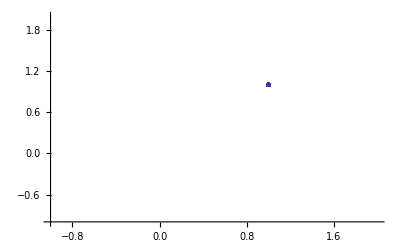

```mathematica
ListPlot[answerVUVDList,AxesOrigin->{-1,-1}]
```

Dist of voteups

Histogram::hbins: The bin specification 150 cannot be used to determine either how many or which bins to use.

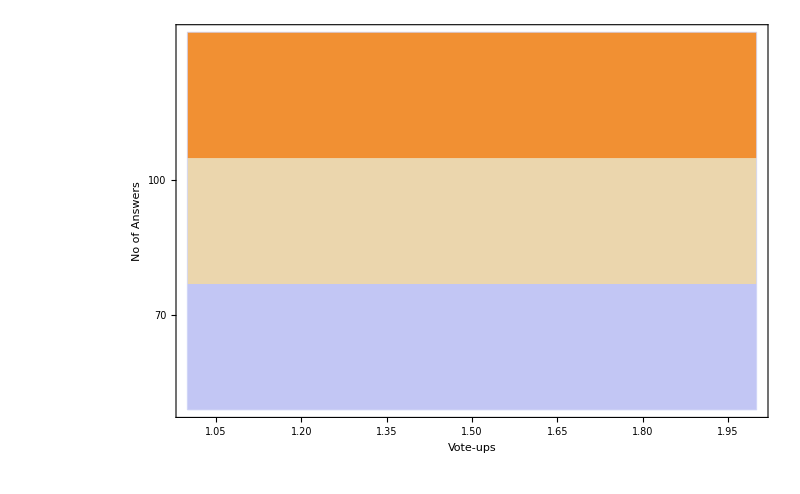

```mathematica
answerVUHisLog=Histogram[answerVU,answerURLListLen+2,ChartElementFunction->"GradientScaleRectangle",ScalingFunctions->"Log",Frame->True,FrameLabel->{"Vote-ups","No of Answers"},ImageSize->800]
```

Histogram::hbins: The bin specification 148 cannot be used to determine either how many or which bins to use.

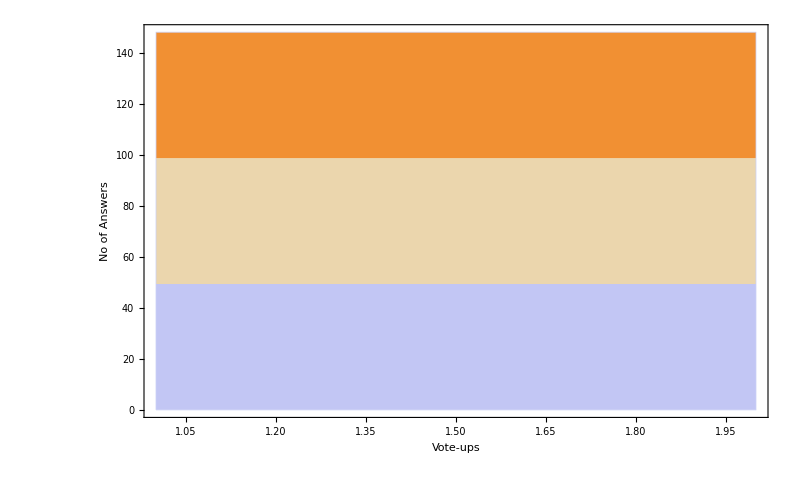

```mathematica
answerVUHis=Histogram[answerVU,answerURLListLen,ChartElementFunction->"GradientScaleRectangle",Frame->True,FrameLabel->{"Vote-ups","No of Answers"},ImageSize->800]
```

```mathematica
answerTableCompleteHead=Grid[{{ImageResize[userIMG,70],Style[userID,30]},{SpanFromAbove,"总回答数："<>ToString[answerURLListLen]<>"； "<>"总支持数："<>ToString[answerSupLen]<>"； "<>"总反对数："<>ToString[answerDownLen]<>"；"<>"平均支持数"<>ToString[answerSupAvg]<>"；"<>"(生成时间："<>DateString[{"Day","-","Month","-","YearShort"}]<>")"}}];
```

```mathematica
answerTableComplete=Grid[{{answerTableCompleteHead},{─},{Style["Hisogram",50]},{answerVUHis},{─},{Style["Answers",50]},{answerTable}}];
```

#### Export Data

Export The Results

```mathematica
(*
answerExpXLS=Export["Export/"<>"USR"<>ToString[userID]<>"_Answers_"<>DateString[{"Day","-","Month","-","Year"}]<>".xls",answerTableLink]
*)
```

Export/USRC.CristataX_Answers_18-07-2013.xls

```mathematica
answerExpPDF=Export["Export/"<>"USR"<>ToString[userID]<>"_Answers_"<>DateString[{"Day","-","Month","-","Year"}]<>".pdf",answerTable,"PDF"]
Remove[answerExpPDF]
```

Export/USRC.CristataX_Answers_18-07-2013.pdf

```mathematica
answerExpCSV=Export["Export/"<>"USR"<>ToString[userID]<>"_Answers_"<>DateString[{"Day","-","Month","-","Year"}]<>".csv",answerGridTable,"CSV"]
Remove[answerExpCSV]
```

Export/USRC.CristataX_Answers_18-07-2013.csv

```mathematica
(*
answerExpIMG=Export["Export/"<>"USR"<>ToString[userID]<>"_Answers_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",answerTable]
Remove[answerExpIMG]
*)
```

```mathematica
answerExpVUHis=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersVUHis_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",answerVUHis]
```

Export/USRC.CristataX_AnswersVUHis_18-07-2013.png

```mathematica
answerCompleteExpPDF=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersCompletePDF_"<>DateString[{"Day","-","Month","-","Year"}]<>".pdf",answerTableComplete,CharacterEncoding->"UTF-8"]
Remove[answerCompleteExpPDF]
```

Export/USRC.CristataX_AnswersCompletePDF_18-07-2013.pdf

```mathematica
answerCompleteExpSVG=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersCompletePDF_"<>DateString[{"Day","-","Month","-","Year"}]<>".svg",answerTableComplete,CharacterEncoding->"UTF-8"]
Remove[answerCompleteExpSVG]
```

Export/USRC.CristataX_AnswersCompletePDF_18-07-2013.svg

```mathematica
answerCompleteExpRTF=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersCompletePDF_"<>DateString[{"Day","-","Month","-","Year"}]<>".rtf",answerTableComplete,CharacterEncoding->"UTF-8"]
Remove[answerCompleteExpRTF]
```

Export/USRC.CristataX_AnswersCompletePDF_18-07-2013.rtf

## Answer Content

```mathematica
ansConList=ParallelTable[{StringCases[Import[answerURLListT[[i]],"Source"],"<h1 id=\"articleTitle\">"~~__~~"</h1>"],StringDrop[StringCases[Import[answerURLListT[[i]],"Source"],"<div itemprop=\"http://rdfs.org/sioc/ns#content\" class=\"answer-txt answerTxt\">"~~__~~"</div>"~~__~~"<div class=\"cmts cmtsBody\">"],-27]},{i,1,answerURLListLen}];
```

```mathematica
Length[ansConList]
```

1004

```mathematica
ansConList[[1]][[2]]
```

{<div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">首先楼主大致暴露年龄了啊<br />
然后“据说”的内容完全不靠谱啊。不管原作者是谁，基本可以判定其不但不懂经济学，还看了太多《读者》类似物啊。<br />
<br />
根据wiki <a href="http://zh.wikipedia.org/wiki/%E4%BA%94%E5%A4%A9%E5%B7%A5%E4%BD%9C%E5%88%B6">http://zh.wikipedia.org/wiki/五天工作制</a><br />
1994年3月，中国大陆试行“隔周五天工作制”。1995年3月25日，时任国务院总理李鹏签署国务院第174号令，发布《国务院关于修改〈国务院关于职工工作时间的规定〉的决定》，落实自1995年5月1日起，实行五天工作制，即职工每日工作八小时，每星期工作四十小时。学校、医院门诊、企业等也相继跟随。换句话说，1年共有256个工作日。<br />
<br />
五天工作制跟劳动生产率没有半毛钱关系，一定要追究的话，可能与1929年的大萧条有关。当时为了稳定社会情绪，降低用工成本，企业主对员工采取某种形式的“停薪留职”，即每周多放一天假，但是这一天不支付工资。而六天工作制，很可能与旧约中，上帝六天创造世界，第七天休息的神话有关。<br />
<br />
且不论“据说”中对于生产率的描述有多离谱，经济学的常识是在讨论的供给的时候就要讨论需求。欧美国家的需求比中国高的很明显。或者说，欧美国家的需求与供给大致是均衡的，这种均衡体现为一种较高的生活水平。悉尼作为澳洲最发达的城市之一，想靠工资买房也是30年房贷！！！所以，劳动生产率影响的是生活水平，跟工作时长没有半毛钱关系。</div>
                
                }

```mathematica
ansConExp=Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersContent_"<>DateString[{"Day","-","Month","-","Year"}]<>".pdf",ansConList,"PDF"]
```

Export/USR橡胶万岁_AnswersContent_30-05-2013.pdf

```mathematica
Remove[ansConExp]
```

```mathematica
ansConFlatHead="
<?xml version=\"1.0\" encoding=\"UTF-8\"?>
<!DOCTYPE html PUBLIC \"-//W3C//DTD XHTML 1.1 plus MathML 2.0//EN\"
        \"HTMLFiles/xhtml-math11-f.dtd\">

<!-- Created by Wolfram Mathematica 8.0 : www.wolfram.com -->

<html xmlns=\"http://www.w3.org/1999/xhtml\">
<head>
    <meta charset=\"UTF-8\"><title>"<>ToString[userID]<>"</title></head><body>";
ansConFlatFoot="</html>";
```

```mathematica
ansConFlat="ansConFlatHead"<>ToString[Flatten[ansConList]]<>"ansConFlatFoot";
```

```mathematica
ansConPlain=StringReplace[Flatten[ansConList],"<"~~Except[">"]..~~">"->""];
```

```mathematica
Export["Export/"<>ToString[userID]<>"/USR"<>ToString[userID]<>"_AnswersContentData_"<>DateString[{"Day","-","Month","-","Year"}]<>".pdf",ansConPlain]
```

Export::nodir: Directory "C:\\USERS\\Guokr\\Documents\\GitHub\\WhyMathematica\\Web\\WebExtraction\\UserAnswersGuokr\\Export\\\:6a61\:80f6\:4e07\:5c81\\" does not exist.

Export::noopen: Cannot open "Export/\:6a61\:80f6\:4e07\:5c81/USR\:6a61\:80f6\:4e07\:5c81_AnswersContentData_30-05-2013.pdf".

$Failed

```mathematica
Export["Export/"<>"USR"<>ToString[userID]<>"_AnswersFullXLS_"<>DateString[{"Day","-","Month","-","Year"}]<>".xls",ansConList]
```

Export/USREnt_AnswersFullXLS_31-05-2013.xls

## Draft Temp

```mathematica
answerTitleList=Table[Cases[Import[urlAnswersList[[i]],"XMLObject"],XMLElement["h2",{},{XMLElement["a",{"shape"->"rect","target"->"_blank","href"->qurl_},{title_}]}]:>{qurl,title},Infinity],{i,1,Length[urlAnswersList]}];
```

{{{http://www.guokr.com/question/376240/,温度有没有一个最高值？},{http://www.guokr.com/question/465587/,窗帘能制作可以使用的降落伞吗？},{http://www.guokr.com/question/463910/,果壳有哪些与太空天气（太阳风暴等）有关的好问答？},{http://www.guokr.com/question/463838/,孪生素数猜想是什么？它在数学上有怎样的意义？},{http://www.guokr.com/question/461852/,物理学中的作用量是什么意思？},{http://www.guokr.com/question/463740/,如果每个概念仅限200字，你能够解释清楚哪些自己专业的概念呢？},{http://www.guokr.com/question/463637/,你所知道的具有警示性的实验室事故有哪些？},{http://www.guokr.com/question/462848/,如何找到落在地球上的陨石的记录呢？},{http://www.guokr.com/question/462722/,夏天来了，网上不少帖子说穿红色衣服更能吸收紫外线，因为红色光波离紫外线是可见光中最远的，这种说法貌似有理，求真相？}},{{http://www.guokr.com/question/462416/,各个国家的法定结婚年龄是什么样的？},{http://www.guokr.com/question/459449/,如果核聚变只能是平均核子质量变小，那么我们宇宙中的铁以上的重元素是怎么来的呢？},{http://www.guokr.com/question/462007/,计算韩国小姐脸相似度的算法是什么？},{http://www.guokr.com/question/462000/,流星雨有哪些观测方法？},{http://www.guokr.com/question/461999/,某个星座的流星雨是什么意思？},{http://www.guokr.com/question/461981/,为什么我求出来的这个积分式子的两组上下限最后得出的结果不同呢？},{http://www.guokr.com/question/461925/,系外行星（Exoplanet）有哪些漂亮的数据可视化？},{http://www.guokr.com/question/461922/,关于系外行星（Exoplanet）有哪些有用的网站？},{http://www.guokr.com/question/461917/,系外行星（Exoplanet）的主要的发现手段是什么？},{http://www.guokr.com/question/457924/,如果知道出租车的GPS，做数据挖掘，能得到什么？}},{{http://www.guokr.com/question/454083/,为什么石子或水滴击打水面形成的水波往外越来越小？},{http://www.guokr.com/question/437067/,任意图形都能用函数形式表示出来么?},{http://www.guokr.com/question/461054/,你用过的最好的在线支持 TeX/LaTeX 的公式编辑器是什么？},{http://www.guokr.com/question/461079/,请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？},{http://www.guokr.com/question/460375/,小行星上的资源真的很多么？},{http://www.guokr.com/question/232028/,目前人类有在太空里做过OOXX且受孕之类的事情吗？},{http://www.guokr.com/question/460024/,我是一个内向的人，有哪些果壳的问答是跟我相关的呢？},{http://www.guokr.com/question/459783/,你所学的专业中，有哪些特别有效的分析和解决问题的方法？},{http://www.guokr.com/question/459256/,要从高空（卫星轨道）扔下无动力的钨钢棒命中一个地面目标需要考虑那些因素？},{http://www.guokr.com/question/459235/,《特种部队：全面反击》中能够把铁丝网烧断的手套是什么原理？}},{{http://www.guokr.com/question/459185/,电子设计方面（模拟技术、电源技术等）有什么好一点的国外论坛，问答网站更好？},{http://www.guokr.com/question/457972/,做网页适应屏幕有多难？},{http://www.guokr.com/question/457826/,用python的前辈们，pylab是matplotlib的一个模块吗，跟pyplot又是什么关系呢？},{http://www.guokr.com/question/457820/,微分几何中坐标为何是光滑函数？},{http://www.guokr.com/question/457189/,为什么刚睡醒时还记得的梦，很快就会把细节忘掉？},{http://www.guokr.com/question/457675/,为什么早上没睁眼的时候记得刚做的梦，一起来就忘完了呢？},{http://www.guokr.com/question/457725/,有人说键盘辐射量最高，应为他有很多个小开关，是真的吗？要怎么理解？},{http://www.guokr.com/question/457536/,双相情感障碍是什么，属于精神问题吗？},{http://www.guokr.com/question/457487/,高铁车顶上取电装置高速运动，不会与电线产生强烈摩擦吗？},{http://www.guokr.com/question/457352/,鸟叔新mv里，放屁用手接住然后在别人脸前摊开，是否真的可行？ 这股空气能在手中保持多久，不会扩散吗？}},{{http://www.guokr.com/question/457031/,银行卡等其他储值卡和手机放在一起是否会消磁，如果会安全距离是多少？},{http://www.guokr.com/question/457299/,为什么宇航员不能在太空中流泪？},{http://www.guokr.com/question/457302/,果壳有哪些跟欧拉有关的内容？},{http://www.guokr.com/question/456650/,这个怎么算？},{http://www.guokr.com/question/456657/,为什么数独题的数字摆放都是中心对称的（不知道用“都”合适不合适，起码我手里的都是）？为了美观还是为了确保没有无限解？},{http://www.guokr.com/question/456216/,巴西果效应确实存在吗？研究发现，在地球上，大坚果上升到表面的速度比火星上更快…},{http://www.guokr.com/question/380115/,钢铁侠中自创新元素靠谱么？},{http://www.guokr.com/question/456557/,在海军军舰上有的挂了一大排旗，有点像万国旗，它们是什么？},{http://www.guokr.com/question/392633/,钢铁侠把头盔戴上后是怎样看清里面的？},{http://www.guokr.com/question/456383/,量子反常霍尔效应是什么意思，它有什么作用？}},{{http://www.guokr.com/question/456375/,如果人类的屁和天然气一样易燃，今天的世界会是怎样？},{http://www.guokr.com/question/455806/,《安德的游戏》中为什么会要选择小孩子来作为指挥官呢？},{http://www.guokr.com/question/455974/,《安德的游戏》中有哪些很奇异的科技？},{http://www.guokr.com/question/455968/,《安德的游戏》中的重要的机构都在哪里？（例如IF指挥学院）},{http://www.guokr.com/question/455970/,《安德的游戏》中都提到了安德的哪些战略战术？},{http://www.guokr.com/question/455969/,《安德的游戏》中虫族是什么样的生物？},{http://www.guokr.com/question/455899/,如果有一个内表面是光滑镜面的球壳，一个人呆在球里面会看到什么？},{http://www.guokr.com/question/455550/,互联网的总存量是多少才能容得下这么多网站？},{http://www.guokr.com/question/455520/,离子推进器（Ion Thruster）是什么？},{http://www.guokr.com/question/455423/,vim 到底好在哪里？}},{{http://www.guokr.com/question/454746/,罗盘不停的乱转是怎么造成的？},{http://www.guokr.com/question/454745/,《星际传奇》第一部的星系有什么特点？},{http://www.guokr.com/question/356801/,绝对零度是永远不可能达到的吗？},{http://www.guokr.com/question/454755/,有没有关于盖亚假说的科幻经典作品，望列单},{http://www.guokr.com/question/454752/,为什么人们能精确预测几十年后的日食，却没法“精确”预测明天的天气？},{http://www.guokr.com/question/454735/,有哪些很棒的一图胜千言的例子？},{http://www.guokr.com/question/413439/,宇宙是一个生命体，而地球是当中的某个器官，地球上的所有东西是它的组成部分。所以各种污染阿破坏阿之类的，是地球这个活体在癌变！这是哪个宗教的说法？},{http://www.guokr.com/question/453927/,星系为什么是圆盘状的,人造卫星就可以变成各个方向的},{http://www.guokr.com/question/119480/,如果能量是守恒的，那么启动宇宙的最初的能量是哪来的？},{http://www.guokr.com/question/453983/,1元人民币换算泰铢是多少
}},{{http://www.guokr.com/question/453807/,果壳问答有哪些关于《三体》的好问题？},{http://www.guokr.com/question/453718/,为什么尿到光滑的（男）小便池上的尿会偶尔弹出很高？},{http://www.guokr.com/question/453534/,如何才能改变宇宙的命运？},{http://www.guokr.com/question/453544/,引力波的速度是多少？},{http://www.guokr.com/question/453541/,现实生活中有人在研究曲率引擎吗？},{http://www.guokr.com/question/453538/,研究宇宙学有意义么？},{http://www.guokr.com/question/453530/,为什么我们现在的主流的宇宙理论是宇宙大爆炸学说？},{http://www.guokr.com/question/93483/,哪一句话可以概括你中意学科的特点？},{http://www.guokr.com/question/453165/,XKCD的1190号漫画《Time》改如何理解？},{http://www.guokr.com/question/453361/,太阳系周围有些什么东西？}},{{http://www.guokr.com/question/453325/,如何简洁明了的解释太阳系的结构？},{http://www.guokr.com/question/453169/,房间内无需电源的电器可以实现么?},{http://www.guokr.com/question/453148/,《三体》2中章北海太空猎杀场景中隔五千米击中目标人物的难度有多大？},{http://www.guokr.com/question/453106/,你最喜欢海子哪段诗歌？},{http://www.guokr.com/question/452978/,我一年只上1天班？  下边这个算法的谬误之处在哪里啊？},{http://www.guokr.com/question/452959/,《宇宙中的邪恶轴心》文中提到的背景辐射可以被星系拉长该如何理解呢？},{http://www.guokr.com/question/452365/,最新的 PLANCK 卫星的数据显示宇宙的年龄是138亿年的数据是如何得出的？},{http://www.guokr.com/question/452371/,什么是微波背景辐射？},{http://www.guokr.com/question/452372/,宇宙微波背景辐射会对影响人们的身体健康么？},{http://www.guokr.com/question/452236/,天文照片 false color 照片上色有没有什么约定俗成的规则？}},{{http://www.guokr.com/question/452223/,极化率那个符号大家都是怎么写的？},{http://www.guokr.com/question/452024/,在太空流鼻血，血液会不会因为心脏给的压力而猛冲出来，然后把宇航员反推到墙上？},{http://www.guokr.com/question/452083/,宇航员在太空中失去动力可以通过自断手臂喷出血液来运动到近处的飞船么？},{http://www.guokr.com/question/452030/,烟花打入水中也能炸开吗？},{http://www.guokr.com/question/452039/,存在真正的同一平面非共点力吗?物体受到力的作用后就要发生形变力的延长线就会相交，还是说同一平面的非共点力，只是人们想象出来的？},{http://www.guokr.com/question/452052/,《三体》中提到的论文《太阳系内新的强发射源》是真实存在的么？},{http://www.guokr.com/question/452015/,一个苹果的引力能改变光的方向吗？},{http://www.guokr.com/question/445872/,为什么无线电波频率的高低与发射者被定位的可能性有关？},{http://www.guokr.com/question/451740/,水流倒流是怎么回事？还能够旋转起来，原理究竟是怎么样的呢？有物理帝解释下么？},{http://www.guokr.com/question/375909/,恒星温度与颜色的有什么关系？}},{{http://www.guokr.com/question/302026/,关于光速（相对论）},{http://www.guokr.com/question/180666/,怎么快捷地向人解释相对论？},{http://www.guokr.com/question/451241/,笔记本键盘能不能改成带灯的？},{http://www.guokr.com/question/448211/,如果建造长度伸出太阳系的太空电梯，岂不是以步行的速度就能逃出《三体》黑域？},{http://www.guokr.com/question/305809/,《三体Ⅲ》中相对论导致的时间变慢怎么理解？},{http://www.guokr.com/question/385292/,听《三体2》的时候想起一问题：“云天明和云天河什么关系？”},{http://www.guokr.com/question/380622/,暗能量负压强是什么意思？},{http://www.guokr.com/question/294925/,暗能量是什么东西？},{http://www.guokr.com/question/450977/,请问一个铁原子面对磁铁，与铁面对磁铁，有什么不同？},{http://www.guokr.com/question/450758/,Einstein 的广义相对论一定是对的么？}},{{http://www.guokr.com/question/450756/,我们如何得知自己处在银河系的什么位置？},{http://www.guokr.com/question/431218/,为什么扔飞刀拿的是刀刃？},{http://www.guokr.com/question/446017/,引力常量的测量有是不是忽略了周围的东西？},{http://www.guokr.com/question/448173/,真实的宇宙恐怕并不是我们看（观察）到的或（/和）推断出的景象吧？}}}

```mathematica
Import[answerURLListT[[1]],"Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

```mathematica
Import[answerURLListT[[1]],"Source"]
```

<!DOCTYPE HTML>
<html lang="en">
<head>
    <meta charset="UTF-8">
    <title>温度有没有一个最高值？ | 问答 | 果壳网 科技有意思</title>
    <meta name="Keywords" content="物理学,热力学,温度,果壳,果壳网,科技,泛科技,智趣,生活,科普"/>
    <meta name="Description" content="温度有没有一个最高值？"/>
    
    
    
    <link rel="stylesheet" type="text/css" href="http://static.guokr.com/skin/gui.css?v=3df592b569e9">
    
    <link rel="stylesheet" type="text/css" href="http://static.guokr.com/skin/ask.css?v=d641db315ef6" />

</head>
<body>
    <div itemscope itemtype="http://rdfs.org/sioc/types#Answer" class="container ">
        <div class="guokr" id="guokr"></div>
        <div class="gheader-wp">
            
            <div class="gheader-wp-b">
                <div class="gheader" id="gheader">
                    
                    <a class="gheader-logo gfl" id="guokrLogo" href="http://www.guokr.com/" title="果壳 科技有意思">果壳网</a>
                    <form id="search" class="gsearch" action="http://www.guokr.com/search/all/" method="get" target="_blank">
                        <p>
                            <input id="searchTxt" class="gsearch-txt" type="text" value="" placeholder="" maxlength="30" name="wd">
                            <input class="gsearch-bt gicon-search" type="submit" value="搜索">
                        </p>
                    </form>
                    
                    
                    <ul class="gnav gfl">
                        <li><a href="http://www.guokr.com/">首页</a></li>
                        <li><a href="http://www.guokr.com/site/">主题站</a></li>
                        
                        <li><a href="http://www.guokr.com/group/hot_posts/">小组</a></li>
                        
                        <li><a href="http://www.guokr.com/ask/">问答</a></li>
                        <li><a href="http://www.guokr.com/event/all/">活动</a></li>
                    </ul>
                    <div class="gheader-i gfr">
                    
                        
                        <a href="https://account.guokr.com/sign_up/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382">注册</a>
                        <a class="gheader-i-sp">|
                        </a><a href="https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&amp;redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F493037%2F&amp;response_type=cookie&amp;client_id=32382">登录</a>
                        
                    
                    </div>
                    
                </div>
            </div>
            
        </div>

        
    <div class="grow gmt30 ask-content-page">
        <div class="main gspan-21">
            <div class="gbreadcrumb">
                <ul>
                    <li>
                        <a itemprop="http://rdfs.org/sioc/ns#has_space" href="http://www.guokr.com/ask/">问答</a>
                    </li>
                    <li>
                    
                        温度有没有一个最高值？
                    
                    </li>
                </ul>
            </div>
            
    
    <meta itemprop="http://rdfs.org/sioc/ns#link" content="http://www.guokr.com/answer/493037/redirect/" />
    <div class="post">
        <div class="post-title">
            <h1 id="articleTitle">温度有没有一个最高值？</h1>
        </div>
        
        <p class="post-tags tags" id="tags">
        
            
            <span class="tag"><a href="http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86%E5%AD%A6/" data-id="物理学">物理学</a></span>
            
            <span class="split">|</span>
            
        
            
            <span class="tag"><a href="http://www.guokr.com/ask/tag/%E7%83%AD%E5%8A%9B%E5%AD%A6/" data-id="热力学">热力学</a></span>
            
            <span class="split">|</span>
            
        
            
            <span class="tag"><a href="http://www.guokr.com/ask/tag/%E6%B8%A9%E5%BA%A6/" data-id="温度">温度</a></span>
            
        
        </p>
        <div class="post-detail" id="articleContent">
            <p id="questionDesc">理论上，有没有一个最高的温度，在达到这个温度（或之前），能量将必须以其它形式释放出去？
            </p>
        </div>
        <div class="cmtsBody" id="questionCmts">
            
            
        </div>
    </div>
    <div class="single-share-box">
        
        <div id="singleAnswerTopShare" class="single-answer-top" data-answerId="493037" data-nickname="时见疏星" data-time="1369737459" data-xlnickname="@星河逍遥"></div>
        

        <p>
            <a itemprop="http://rdfs.org/sioc/ns#reply_of" href="http://www.guokr.com/question/376240/">查看全部12个答案</a>
        </p>
    </div>
    <div class="answers" id="answers">
        
            
                    
        <div itemprop="http://rdfs.org/sioc/ns#has_disccussion" itemscope itemtype="http://schema.org/UserLike" class="ghide">
            <meta itemprop="description" content="41" />
        </div>
        <div itemprop="http://rdfs.org/sioc/ns#has_disccussion" itemscope itemtype="http://schema.org/UserBlocks" class="ghide">
            <meta itemprop="description" content="0" />
        </div>
        <div class="answer " id="answer493037">
            <div class="answer-digg digg">
                <a href="javascript:void 0;" data-operation="support" data-id="493037" class="answer-digg-up" title="支持（+1）">41</a>
                <a href="javascript:void 0;" data-operation="oppose" data-id="493037" class="answer-digg-dw" title="反对(-1)">0</a>
            </div>
            <div class="answer-r">
                <div class="answer-t">
                    <a class="answer-img" href="http://www.guokr.com/i/1769480175/" title="时见疏星" target="_blank">
                        <img width="24" height="24" src="http://img1.guokr.com/thumbnail/TcCEQCVVXmDne6eXJv4nOu5LSGuaqh_kjG6U_NfdSi-gAAAAoAAAAEpQ_24x24.jpg">
                    </a>
                    <p class="answer-usr">
                        <a itemprop="http://rdfs.org/sioc/ns#has_creator" class="answer-usr-name" href="http://www.guokr.com/i/1769480175/" title="时见疏星" target="_blank">时见疏星</a>理论物理专业，西夏文爱好者<a class="gicon-sai" title="果壳达人" href="/nuts/" target="_blank">ψ</a>
                    </p>
                    <meta itemprop="http://purl.org/dc/terms/modified" content="2013-05-26T21:28:39.142343+08:00" />
                    <p class="answer-date">2013-05-26 21:28</p>
                </div>
                <div class="answer-diggers diggers" data-id="493037">
                    
                    支持者：
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/1400697749/">-无语森-</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/1734233484/">姬十三</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/0149506085/">洛雪_ChaCha</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/0526308343/">MrRaindrop</a>
                            </span>
                            
                        
                            
                            <span>
                                <a href="http://www.guokr.com/i/1240786300/">LAughmoon</a>
                            </span>
                            
                        
                        
                        <a href="javascript:void 0;"
                            data-operation="expandDiggers"
                            class="answer-diggers-all" data-id="493037">更多<span></span></a>
                        
                    
                </div>
                <div itemprop="http://rdfs.org/sioc/ns#content" class="answer-txt answerTxt">如果只看一个简短的答案：<br />
<br />
<br />
<strong>单从数学上比较数字大小来理解：</strong><br />
<br />
若这个上限指的是所有的可能情况中都不能达到的，那么没有。<br />
<br />
如果这个上限指的是某些体系不能达到的，那么是有的。<br />
<br />
<strong>从物理上来看：</strong><br />
<br />
总会有个上限，而且至少有两种情况的上限。<br />
<br />
<br />
<br />
（如果只想看简短的解释，可以从 为什么要说这么复杂 这部分开始看）<br />
<br />
<br />
=====<br />
<br />
其实如果不理解温度是什么，回答这个问题就会有问题。所以先废话一下，说说温度是什么。<br />
<br />
## 温度是什么<br />
<br />
温度一般是通过热力学来定义的，当然热力学要通过统计物理来看本质。<br />
<br />
热力学定义温度，需要用到第零定律和第二定律，一个给出了最基本的物理意义（平衡和冷热程度），一个给出了定量的描述（可以给出温度标准）。<br />
<br />
<br />
那么冷热程度是什么意思呢？我们常说温度在平衡态的时候从有意义，虽然不尽然如此，但是平衡态下，温度确实有个比较好的定义。为什么呢？因为我们借助于平衡态来定义温度。<br />
<br />
## 冷热程度<br />
<br />
想想我们用温度计来测量一个物体的温度，然后用同一只温度计测量另一个物体的温度。如果温度计都是显示 50 摄氏度，那么我们就说这两个物体都是 50 摄氏度。<br />
那么我们又为什么敢下结论说两个物体的温度都是 50 摄氏度呢？这是因为我们有第零定律：<br />
<blockquote><span style="color: #999999;">若两个热力学系统均与第三个系统处于热平衡状态，此两个系统也必互相处于热平衡。</span></blockquote>
这是一种传递性。<br />
<br />
如果你在夏天的时候跟一个大冬瓜相拥入睡，假设你跟冬瓜达到了热平衡状态。然后你女朋友/男朋友也更这个冬瓜相拥，发现你女朋友/男朋友已经是跟冬瓜答道平衡状态了。这样我们就可以推断你和你的女朋友/男朋友也是平衡状态。<br />
当然，这个道理中，把冬瓜换成温度计，如果你和你的女朋友/男朋友分别跟温度计相拥之后，发现温度计的状态都一样，那么就说明你跟你的女朋友/男朋友那是大和谐了：温度相同，而且处于平衡状态。<br />
<br />
说到这里，有人就想问：<br />
（热）平衡是什么意思？<br />
<br />
热平衡的意思是说，在上面的例子中，你的一部分和你的女朋友/男朋友的一部分交换，或者你给了你的女朋友一部分，或者你的男朋友给了你一部分，从热力学的角度来看，对于这个体系来说，没啥区别。（大和谐嘛）<br />
<br />
那我们如何定量来给出温度的呢？或者温度计背后有着什么样的深刻道理呢？<br />
<br />
<br />
## 温度的定量<br />
<br />
<br />
这个道理就是热力学第二定律。<br />
<br />
这个说起来有点头疼。我试试吧。<br />
<br />
热力学第二定律的最最核心的内容是：<br />
熵是一个状态函数。（熵通常被认为是表示体系的混乱程度的一个量，状态函数的意思是说，熵至于体系的状态有关，而跟如何达到这个状态是无关的。）<br />
<br />
那又如何呢？我们可以通过总结建立起熵和温度的关系式，如果熵是一个状态函数，那我们就可以定量了，因为这样就可以一个温度对应一个状态了。<br />
<br />
（要知道我们给出温度的定量严格的说，需要利用可逆过程。然而这东西说起来就是讲一节课了。）<br />
<br />
我知道我知道，这样说好像很难理解。所以我们还是来看看另一种说法。<br />
<br />
假定你和你的男朋友/女朋友分别是高温的提供热量的源泉和低温的用来冷却的源泉，那么可以利用你们二人的温度差异来对外做功，向外界提供能量。我们可以找到一类理想的特定的过程，这类过程中，你们二人对外做功的效率至于你们二人的温度有关，可以写成<br />
<img src="http://img1.guokr.com/formula/50d20f946797ecbe3bcdfbdc536c989108a1464d.png" class="edui-faked-insertmathjax" data-code="\eta=1-\frac{T_{You}}{T_{TA}}" style="max-width: 480px" /><br />
效率 = 1-你的温度 / 你女朋友/男朋友的温度<br />
<br />
利用这样的跟过程相关的手段，我们可以建立起热力学的温度计量。<br />
<br />
<br />
## 为什么要说这么复杂<br />
<br />
上面这两部分，主要是说明热力学里面温度确实是跟组成物理的粒子的混乱程度或者这些粒子运动的状态有关：物体运动越剧烈，温度就越高。<br />
<br />
那么剧烈程度是什么意思呢？在物理上将，这个是指的分子的动能。动能大的粒子越多，温度就越高。<br />
<br />
那么如果运动太剧烈了呢？会触及到相对论的情况么？<br />
<br />
答案是会的。<br />
<br />
<strong>在广义相对论课上，基本上会有这样一个习题，就是问，能量密度多大会变成黑洞。这个是可以算的。</strong><br />
<strong>也就是说，一个区域内的能量太大，会导致能量密度太高，这样就是黑洞了。这样体系就变成了另一种描述，不是原来的体系了，所以我们说，原来那个体系，所能达到的最高的温度是有个上限的。</strong><br />
<br />
<br />
## 为什么是运动的剧烈程度<br />
<br />
为什么温度是用分子的运动的动能来衡量的呢？起初看来这个问题像是牛角尖。但是仔细思考之后，会发现一个更深刻内容。（进入统计的领域）<br />
<br />
我们上面提到了温度和熵有关系，他们可以这样写出来：<br />
<img src="http://img1.guokr.com/formula/01cc3b8141b83773530475028310f4878cd2b3fe.png" class="edui-faked-insertmathjax" data-code="\frac{1}{T}=\left(\frac{\partial S}{\partial U}\right)_{Y}" style="max-width: 480px" /><br />
<br />
温度的倒数 = 熵对内能的偏导数<br />
<br />
公式没什么用，这个公式只是告诉我们，温度是随着体系混乱程度跟随体系内能的变化快慢相关的，如果体系的混乱程度不随体系的内能变化的时候，也就是右边变成了 0，那么温度就到了无穷了。<br />
<br />
对于我们通常想到的情况，也就是体系的内部能量是通过分子的运动来体现的情况，因为体系内能越大，就越混乱（状态数越多），这个非常合理，温度永远大于零。（这个最本质的原因还是因为玻尔兹曼统计）只是如果太极端，这个会遇到相对论的限制，达到一个上限。<br />
<br />
哎呀，我们忽略了量子的情况。也就是说，如果内部的能量不是通过这种连续的分子的运动来实现的，而是每个例子只有两种可能的能量状态。那么这时候，就需要另外考虑了，假定我们可以用手摆出一种状态，这种状态里面，能量高的粒子要比能量低的例子多，这样当我们去增加体系内部的能量，也就是去把能量低的粒子放到能量高的位置上的时候，会发现，体系的混乱程度是减小的（状态数的减少），如此一来，这个体系的温度就会变成负的。而可以想到，在正和负的交接处，我们可以用手摆出温度为无穷的情况。<br />
<br />
或者，不去理解这个现象，只作为知识记住的话，应该看一下下面的图：<br />
<img src="http://img1.guokr.com/image/YVk4HWbsod_vOOPqaCLH3CzEcs7LAGU0EtKmwCh-OWjCAQAALQEAAFBO.png" style="max-width: 480px" /><br />
（汪志诚老先生<a href="http://book.douban.com/subject/1130137/">《热力学·统计物理》</a> 第三版，P285 ）<br />
<br />
不管这个图的横轴，只需要知道，温度从低到高的顺序是：<br />
+0 -&gt; 正无穷 -&gt; 负无穷 -&gt; -0<br />
<br />
这样说，温度也有个上限。<br />
<br />
<br />
<br />
## 总结<br />
<br />
总之，不论如何，温度总会有个上限，不同的是，有两种情况：<br />
一种是受到相对论对能量密度的限制<br />
一种是完完全全的统计给出的，普适的，无条件的上限。<br />
<br />
</div>
                
                <div class="cmts cmtsBody">
                    <div class="cmts-t cmtsTitle">
                        <p class="gfl">
                            <a href="javascript: void 0;" data-operation="control" data-id="493037" data-question="0" class="cmts-num">20条讨论</a>
                            
                        </p>
                        
                    </div>
                    <div class="ghide cmtsList cmts-bd gclear">
                        <b class="arrow_up">
                            <s class="arrow_up"></s>
                        </b>
                        <div class="cmts-do cmtsDo">
                            <textarea name="cmt" rows="10" cols="30" class="gbtxt"></textarea>
                            <p>
                            <a href="javascript:void 0;" class="cancel-cmt" data-operation="cancelCmt">取消</a>
                                <input type="submit" value="讨论" class="gbtn-primary" data-operation="answerCmt" data-question="0" data-id="493037" data-type="answer">
                            </p>
                        </div>
                        <ul class="cmts-list"></ul>
                    </div>
                </div>
            </div>
        </div>

        <div id="singleAnswerBottomShare" class="single-answer-bottom" data-answerId="493037" data-nickname="时见疏星" data-time="1369737459" data-xlnickname="@星河逍遥"></div>
        

        <div class="main-recommend-questions gclear">
            <div class="recommend-best-question gfl" id="recommendQuestionBest">
                <h2>最佳问答</h2>
                
                <p>
                <a href="http://www.guokr.com/question/436820/" title="为什么果壳网突然变样了？上面的果壳达人也没了？" target="_blank">为什么果壳网突然变样了？上面的果壳达...</a>7回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/436911/" title="非专业人士通常对法医有哪些误解？法医有哪些不为外人所知的秘技（知识）？" target="_blank">非专业人士通常对法医有哪些误解？法医...</a>4回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/436896/" title="生态堆肥厕所如何控制排泄物的转化质量？涉及哪些原理和工艺？" target="_blank">生态堆肥厕所如何控制排泄物的转化质量...</a>2回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/436881/" title="生态堆肥厕所最核心的保证不臭的设计是什么？需要定时维护吗？" target="_blank">生态堆肥厕所最核心的保证不臭的设计是...</a>2回答
                </p>
                
                <p>
                <a href="http://www.guokr.com/question/411445/" title="公司局域网内怎样即时聊天、传文件？" target="_blank">公司局域网内怎样即时聊天、传文件？</a>12回答
                </p>
                
            </div>
            <div class="recommend-relation-question gfr" id="recommendQuestion">
                <h2>热门问答</h2>
                
                <p><a href="http://www.guokr.com/question/292882/" title="霸王龙超短的两只前爪是做什么的？" target="_blank">霸王龙超短的两只前爪是做什么的？</a>38回答</p>
                
                <p><a href="http://www.guokr.com/question/465515/" title="蓝图为什么叫蓝图？是因为蓝色的吗？" target="_blank">蓝图为什么叫蓝图？是因为蓝色的吗？</a>27回答</p>
                
                <p><a href="http://www.guokr.com/question/465803/" title="你见过的果壳成就最NB的是谁？@Ta出来吧！" target="_blank">你见过的果壳成就最NB的是谁？@Ta...</a>13回答</p>
                
                <p><a href="http://www.guokr.com/question/465886/" title="松鼠会2008年成立，果壳网2010年成立，这两个机构的出现给你带来了哪些改变？" target="_blank">松鼠会2008年成立，果壳网2010...</a>23回答</p>
                
                <p><a href="http://www.guokr.com/question/465149/" title="无线路由器附近的植物不发芽，这个实验是真的吗？它科学吗？" target="_blank">无线路由器附近的植物不发芽，这个实验...</a>24回答</p>
                
            </div>
        </div>
    </div>

        </div>
        
            <div class="side gspan-10 gprefix-1">
                <a href="/questions/new/" class="gbtn-primary" id="newPost">提问</a>
                <div class="side-title">
                    <h2>帮助</h2>
                </div>
                <div class="side-question-titles">
                    
                    <p><a href="http://www.guokr.com/question/446444/" target="_blank">在果壳问答如何提问？</a></p>
                    
                    <p><a href="http://www.guokr.com/question/446435/" target="_blank">在果壳问答，应该如何回答问题？</a></p>
                    
                    <p><a href=" http://www.guokr.com/question/436807/" target="_blank">如何插入公式？</a></p>
                    
                </div>
                <div id="bdadm-559153" class="side-advert"></div>
                <div class="side-title mt12">
                    <h2>相关问答</h2>
                </div>
                <div class="side-question-titles" id="recommendQuestionRelated">
                    
                    
                    <p><a href="http://www.guokr.com/question/383522/" title="在绝对零度还不会变固态的是不是只有氦？" target="_blank">在绝对零度还不会变固态的是不是只有氦？</a>2回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/411872/" title="要是有一个物体以6700m/s的速度在运动，它的温度大概是多少？" target="_blank">要是有一个物体以6700m/s的速度在运动，它的温度大概是多少？</a>8回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/362542/" title="温度是否有一个理论上的上界？" target="_blank">温度是否有一个理论上的上界？</a>5回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/458529/" title="低温会降低物体硬度吗？" target="_blank">低温会降低物体硬度吗？</a>2回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/461243/" title="宇宙中有最低温度，那有没有最高温度？" target="_blank">宇宙中有最低温度，那有没有最高温度？</a>1回答</p>
                    
                    
                </div>
                
                <div class="side-advert">
                    <a href="http://www.guokr.com/blog/450829/" target="_blank"><img src="http://img1.guokr.com/image/rHi1ScJ6LWkX8CH06983nHQQUh5NIIGguQnWLaXLMt8iAQAAoAAAAEpQ.jpg" alt="旅游时要注意哪些问题？ — #科学青年速成指南# 第27期" /></a>
                </div>
                
                
                <div class="side-title mt12">
                    <h2>同主题问答</h2>
                </div>
                <div class="side-question-titles" id="recommendQuestionRelevant">
                    
                    
                    <p><a href="http://www.guokr.com/question/317889/" title="木星表面温度那么低，为什么还是气状？" target="_blank" data-gaevent="question_recommend_relevant:question">木星表面温度那么低，为什么还是气状？</a>2回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/293683/" title="太阳的氢如何来的？" target="_blank" data-gaevent="question_recommend_relevant:question">太阳的氢如何来的？</a>3回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/294952/" title="为什么铁在超低温下会变脆？" target="_blank" data-gaevent="question_recommend_relevant:question">为什么铁在超低温下会变脆？</a>1回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/347222/" title="为什么自然界中最低温只能到摄氏零下两百多度，而高温却可以轻易达到几千度呢？" target="_blank" data-gaevent="question_recommend_relevant:question">为什么自然界中最低温只能到摄氏零下两百多度，而高温却可以轻易达到几千度呢？</a>10回答</p>
                    
                    
                    
                    <p><a href="http://www.guokr.com/question/347540/" title="黑体辐射的问题中，辐射频率与温度有关，但温度是指什么的温度？黑体空腔内不是真空只有电磁波吗？" target="_blank" data-gaevent="question_recommend_relevant:question">黑体辐射的问题中，辐射频率与温度有关，但温度是指什么的温度？黑体空腔内不是真空只...</a>2回答</p>
                    
                    
                </div>
                
            </div>
    <script type="text/javascript" src="http://cbjs.baidu.com/js/m.js"></script>
    <script type="text/javascript">
    BAIDU_CLB_fillSlotAsync('559153', 'bdadm-559153');</script>

    </div>


        <div class="gbottom">
    <div class="gbottom-nav">
        <a href="http://www.guokr.com/about/">关于我们</a>
        <a href="http://www.guokr.com/i/0409470284/blogs/">加入果壳</a>
        <a href="http://www.guokr.com/spread/">媒体报道</a>
        <a href="http://www.guokr.com/question/446161/">帮助中心</a>
        <a href="http://www.guokr.com/zone/">内容专区</a>
        <a href="http://www.guokr.com/help/policy/">免责声明</a>
        <a href="http://www.guokr.com/contact/">联系我们</a>
        <a href="http://m.guokr.com/">移动版</a>
        <a href="http://www.guokr.com/mobile/">移动应用</a>
    </div>
    <div class="gbottom-i">©2013果壳网&nbsp;京ICP备09043258号-2&nbsp;京公网安备1101052730</div>
</div>
    </div>
    

    <script type="text/html" id="commentTmpl">
        <li><a href="{url}" target="_blank">{name}</a>：{txt} - {time} <a href="javascript:void 0;" data-id="{id}" data-operation="deleteCmt" class="cmts-list-d">删除</a>&nbsp;<a data-operation="reCmt" href="javascript: void 0;">回复</a></li>
    </script>
       <script type="text/html" id="diggersTmpl">
        <% if (l!=0) { %>支持者：
            <% if (expanded) { %>
                <span>
                    <%for(var i=0;i<l;i++) {
                        if (list[i]) { %>
                            <a href="<%=list[i].url%>"><%=list[i].name%></a>
                            <% if(i<l-1) { %>、<% } %>
                    <% }}%>
                </span>
            <% } else { %>
                <% if (l<=3) { %>
                    <span>
                        <%for(var i=0;i<l;i++) {
                            if (list[i]) { %>
                                <a href="<%=list[i].url%>"><%=list[i].name%></a>
                                <% if(i<l-1) { %>、<% } %>
                        <% }}%>
                    </span>
                <% } else if (l>3) { %>
                    <span>
                        <% for(var i=0;i<3;i++) {
                            if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<2) { %>、<% } %>
                        <% }} %>
                    </span>
                    <a href="javascript:void 0;" data-operation="expandDiggers" data-id="<%=id%>">更多...</a>
                    <span class="hide"><% for(var i=3;i<l;i++) {
                        if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<l-1) { %>、<% } %>
                    <% }} %></span>
                <% } %>
            <% } %>
        <% } %>
    </script>
    <script>
        var g_obj_id = 376240,
            has_answered = false,
            is_admin = false;
    </script>
        
    
   <script>
       
       var g_page_name = "askContentPage",
           GJS_VERSION = 'doom',
           GJS_PRELOAD = ['ga', 'jQuery', 'GUtils', 'api', 'share'],
           ukey = null,
           
           url_signin = "https:\/\/account.guokr.com\/oauth2\/authorize\/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F493037%2F&response_type=cookie&client_id=32382",
           url_signup = "https:\/\/account.guokr.com\/sign_up\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382",
           
           weibo_signin = "https:\/\/account.guokr.com\/weibo\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382",
           renren_signin = "https:\/\/account.guokr.com\/renren\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382",
           qq_signin = "https:\/\/account.guokr.com\/qq\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F493037%252F%26response_type%3Dcookie%26client_id%3D32382";
       
   </script>
   <script src="http://static.guokr.com/js/I.js?v=dc73ae7f4400"></script>
   <script src="http://static.guokr.com/js/main.js?v=d84296f60ddc"></script>
    
    <script src="http://static.guokr.com/js/ask.js?v=81027d63e00a"></script>


</body>
</html>

## Former

### Results

```mathematica
weeklogQTable=Dynamic[Grid[gridTable,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}]]//Quiet
```

```mathematica
weeklogATable=Dynamic[Grid[gridTableAns,Frame->All,Background->{{3->LightOrange,5->LightOrange},{1->LightBlue,2->LightBlue,3->LightGreen}}]]//Quiet
```

### Analyze My Questions | Code

#### Data Import

```mathematica
urlList=StringSplit[StringReplace[Import[queGitSource]," "->""],","]
```

{http://www.guokr.com/question/460295/,http://www.guokr.com/question/460334/,http://www.guokr.com/question/460336/,http://www.guokr.com/question/460339/,http://www.guokr.com/question/460342/,http://www.guokr.com/question/460345/,http://www.guokr.com/question/460379/,http://www.guokr.com/question/460389/,http://www.guokr.com/question/461025/,
http://www.guokr.com/question/461059/,http://www.guokr.com/question/461061/,http://www.guokr.com/question/461089/,
http://www.guokr.com/question/461092/,http://www.guokr.com/question/461246/,http://www.guokr.com/question/461254/,
http://www.guokr.com/question/461261/,http://www.guokr.com/question/461265/,http://www.guokr.com/question/461279/,
http://www.guokr.com/question/461321/,http://www.guokr.com/question/461325/,http://www.guokr.com/question/461330/,
http://www.guokr.com/question/461339/,http://www.guokr.com/question/461335/,http://www.guokr.com/question/460802/,
http://www.guokr.com/question/461121/,http://www.guokr.com/question/461110/,http://www.guokr.com/question/461108/,
http://www.guokr.com/question/461132/}

```mathematica
len=Length[urlList]
```

28

```mathematica
rawData=Table[Import[StringTrim[urlList[[i]]],"XMLObject"],{i,1,len}];
```

```mathematica
expRawData=Export[StringJoin["Data\\RawData","_","Weeklog",ToString[weekLogNum],"_",DateString[{"Day","-","Month","-","YearShort"}],".xml"],rawData,"XML"]
```

Data\RawData_Weeklog6_25-05-13.xml

#### Question Data Analysis

```mathematica
dataSourceQID=Table[Cases[rawData[[i]],XMLElement["input",{"type"->"submit","class"->"gbtn-primary","value"->"讨论","data-operation"->"newCmt","data-question"->"1","data-id"->id_,"data-type"->"question"},{}]:>id,Infinity],{i,1,len}]
dataSourceQDate=Table[StringSplit[StringSplit[Cases[rawData[[i]],XMLElement["span",{"class"->"post-date"},{date_}]:>date,Infinity][[1]],"  "][[2]]][[1]],{i,1,len}]
dataSourceQTitle=Table[Cases[rawData[[i]],XMLElement["meta",{"name"->"Description","content"->title_},{}]:>title,Infinity],{i,1,len}]
```

{{460295},{460334},{460336},{460339},{460342},{460345},{460379},{460389},{461025},{461059},{461061},{461089},{461092},{461246},{461254},{461261},{461265},{461279},{461321},{461325},{461330},{461339},{461335},{460802},{461121},{461110},{461108},{461132}}

{2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-04-28,2013-05-02,2013-05-02,2013-05-02,2013-05-02,2013-05-02,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-05-03,2013-04-30,2013-05-02,2013-05-02,2013-05-02,2013-05-02}

{{薛定谔的猫重要在哪里？},{表情（Emoji）符号的设计需要考虑到哪些因素？},{通过强迫自己处在恐怖的环境中等方式“练胆”起作用么？},{哪些原因可能导致在运动后猝死？},{「水质老化」的说法有道理么？},{喝果汁等含有柠檬酸多的饮料会造成酸血症么？},{土星木星上面不同的颜色的区域是怎么形成的？},{true color 和 natural color 的区别是什么？},{落在地球上的陨石都有哪些来源？},{穿羽绒服可能感染禽流感么？},{今年冬天羽绒服会涨价么？},{「星地量子通信」地基实验是什么？},{地球会因为人类的活动变成金星那样贫瘠么？},{世界上最大的橡皮鸭这件来自荷兰的艺术品该如何品读呢？},{中性氢21厘米辐射是什么？},{为什么我国设置天文系的高校很少？},{21厘米中性氢为什么可以用来探测宇宙的第一屡曙光？},{如果开发出了一个可穿戴的计算设备平台，你能想到哪些比较好玩的应用呢？},{玻璃幕墙的钢化玻璃突然爆裂是什么原因造成的呢？},{钢化玻璃碎片从百米高楼落下来造成的伤害有多大？},{为什么淬火可以让刀剑变得更硬？},{煤矿自燃的原因、预防措施、补救措施是什么？},{为什么森特勒利亚市煤矿起火可以燃烧几十年还不熄灭？},{电网中电压明显突然升高（浪涌）可能是什么原因造成的么？},{物理实验室中有什么鲜为人知的安全指南？},{生物实验室中有什么鲜为人知的安全指南？},{化学实验室中有什么外行人不知道的安全指南？},{人脸混合是怎么算出来的呢？}}

```mathematica
dataSourceA=Table[Cases[rawData[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]}[[2]],Infinity],{i,1,len}]
```

{{3,2},{},{0,0},{},{0},{1,1,1,0},{10,3,0},{},{4,1,0},{6,0},{0,0},{},{},{1,1,0,0,0,0},{4},{1,1,0,0},{},{2,1},{11,3,0,0,0,0,0,0,0},{},{43,12,1,1,0,1,0,0,1,0,0,0,0,0,0,0},{0},{2,0},{2},{3},{4,2,1,1},{3,1,1,0,0},{}}

```mathematica
(*
XMLElement["span",{"class"->"post-date"},{"发表于  2013-04-28 09:56"}]
XMLElement["a",{"shape"->"rect","class"->"cmts-num","href"->"javascript: void 0;","data-question"->"1","data-id"->"460295","data-operation"->"control"},{"添加讨论"}]
XMLElement["meta",{"name"->"Description","content"->"薛定谔的猫重要在哪里？"},{}]
*)
```

```mathematica
lenTotal=Length[DeleteCases[dataSourceA,{}]]
```

20

```mathematica
ansTotal=Length[Flatten[dataSourceA]];
```

```mathematica
supTotal=N[Total[ToExpression[Flatten[dataSourceA]]]];
```

```mathematica
avgAnsPerQ=N[Length[Flatten[dataSourceA]]/len];
```

```mathematica
gridTable=Prepend[Prepend[Prepend[
Sort[Table[{dataSourceQID[[i]][[1]],dataSourceQDate[[i]],Length[dataSourceA[[i]]],dataSourceA[[i]],dataSourceQTitle[[i]][[1]]},{i,1,len}],#1[[3]]>#2[[3]]&]
,{"Question ID","Post Date","Answers","Answer Support","Question Title"}],{"问题数:"<>ToString[len]<>";"<>"有回答的问题:"<>ToString[lenTotal]<>";"<>"回答数:"<>ToString[ansTotal]<>";"<>"总支持："<>ToString[supTotal]<>";"<>"平均回答数："<>ToString[avgAnsPerQ],SpanFromLeft,SpanFromLeft}],{"WeekLog"<>ToString[weekLogNum]<>":"<>"Questions"<>"("<>DateString[{"Day","-","Month","-","YearShort"}]<>")",SpanFromLeft}];
```

### Analyze My Answers | Code

```mathematica
urlListAns=StringSplit[StringReplace[Import[ansGitSource]," "->""],","]
```

{http://www.guokr.com/answer/478727,http://www.guokr.com/answer/480466,http://www.guokr.com/answer/480473,http://www.guokr.com/answer/481224}

```mathematica
lenAns=Length[urlListAns]
```

4

```mathematica
rawDataAns=Table[Import[StringTrim[urlListAns[[i]]],"XMLObject"],{i,1,lenAns}];
```

```mathematica
expRawDataAns=Export[StringJoin["Data\\RawDataAns","Log",ToString[weekLogNum],"-",DateString[{"Day","-","Month","-","YearShort"}],".xml"],rawDataAns,"XML"]
```

Data\RawDataAnsLog6-25-05-13.xml

```mathematica
dataSourceAnsQLink=Table[Cases[rawDataAns[[i]],XMLElement["a",{"shape"->"rect","itemprop"->"http://rdfs.org/sioc/ns#reply_of","href"->url_},{waste_}]:>url,Infinity],{i,1,lenAns}]
dataSourceAnsQDate=Table[StringSplit[Cases[rawDataAns[[i]],XMLElement["p",{"class"->"answer-date"},{date_}]:>date,Infinity][[1]]][[1]],{i,1,lenAns}]
dataSourceAnsQTitle=Table[Cases[rawDataAns[[i]],XMLElement["h1",{"id"->"articleTitle"},{title_}]:>title,Infinity],{i,1,lenAns}]
```

{{http://www.guokr.com/question/460375/},{http://www.guokr.com/question/461079/},{http://www.guokr.com/question/461054/},{http://www.guokr.com/question/437067/}}

{2013-04-28,2013-05-02,2013-05-02,2013-05-03}

{{小行星上的资源真的很多么？},{请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？},{你用过的最好的在线支持 TeX/LaTeX 的公式编辑器是什么？},{任意图形都能用函数形式表示出来么?}}

```mathematica
dataSourceAnsAUp=Table[Cases[rawDataAns[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]},Infinity][[1]],{i,1,lenAns}]
```

{{478727,3},{480466,1},{480473,0},{481224,13}}

```mathematica
lenAnsSup=Total[Table[ToExpression[dataSourceAnsAUp[[i]][[2]]],{i,1,lenAns}]]
```

17

```mathematica
dataSourceAnsADown=Table[Cases[rawDataAns[[i]],XMLElement["a",{"shape"->"rect","class"->"answer-digg-dw","href"->"javascript:void 0;","data-operation"->"oppose","data-id"->labela_,"title"->"反对(-1)"},{labelb_}]:>{labela,labelb},Infinity][[1]],{i,1,lenAns}]
```

{{478727,0},{480466,0},{480473,0},{481224,0}}

```mathematica
lenAnsDown=Total[Table[ToExpression[dataSourceAnsADown[[i]][[2]]],{i,1,lenAns}]]
```

0

Average Vote-ups of my answers

```mathematica
avgAnsMine=N[lenAnsSup/lenAns]
```

4.25

```mathematica
gridTableAns=Prepend[
Prepend[Prepend[
Sort[Table[{dataSourceAnsAUp[[i]][[1]],dataSourceAnsQDate[[i]],ToExpression[dataSourceAnsAUp[[i]][[2]]],dataSourceAnsADown[[i]][[2]],Hyperlink[dataSourceAnsQTitle[[i]][[1]],dataSourceAnsQLink[[i]]]},{i,1,lenAns}],#1[[3]]>#2[[3]]&]
,{"Answer ID","Post Date","Vote-up","Vote-down","Title"}],{"总回答数："<>ToString[lenAns]<>"； "<>"总支持数："<>ToString[lenAnsSup]<>"； "<>"总反对数："<>ToString[lenAnsDown]<>"；"<>"平均支持数"<>ToString[avgAnsMine]<>"；",SpanFromLeft}]
,{"WeekLog"<>ToString[weekLogNum]<>":"<>"Answers"<>"("<>DateString[{"Day","-","Month","-","YearShort"}]<>")",SpanFromLeft}]
```

{{WeekLog6:Answers(25-05-13),},{总回答数：4； 总支持数：17； 总反对数：0；平均支持数4.25；,},{Answer ID,Post Date,Vote-up,Vote-down,Title},{481224,2013-05-03,13,0,},{478727,2013-04-28,3,0,},{480466,2013-05-02,1,0,},{480473,2013-05-02,0,0,}}

### Export Data

Export The Results

```mathematica
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Question_"<>DateString[{"Day","-","Month","-","Year"}]<>".csv",gridTable,"CSV"]
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Answer_"<>DateString[{"Day","-","Month","-","Year"}]<>".csv",gridTableAns,"CSV"]
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Question_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",weeklogQTable]
Export["Export/"<>"WeekLog"<>ToString[weekLogNum]<>"_Answer_"<>DateString[{"Day","-","Month","-","Year"}]<>".png",weeklogATable]
```

Export/WeekLog6_Question_25-05-2013.csv

Export/WeekLog6_Answer_25-05-2013.csv

Export/WeekLog6_Question_25-05-2013.png

Export/WeekLog6_Answer_25-05-2013.png

### Visualizing Data

```mathematica
N[DeleteCases[dataSourceA,{}][[3,2]]/Total[ToExpression[DeleteCases[dataSourceA,{}][[3]]]]]
```

Part::partw: Part 2 of {"0"} does not exist.

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
visData=ToExpression[Table[{Length[DeleteCases[dataSourceA,{}][[i]]],N[DeleteCases[dataSourceA,{}][[i,j]]/Total[ToExpression[DeleteCases[dataSourceA,{}][[i]]]]],DeleteCases[dataSourceA,{}][[i,j]]},{i,1,Length[DeleteCases[dataSourceA,{}]]},{j,1,Length[DeleteCases[dataSourceA,{}][[i]]]}]]/.$Failed->0
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

ToExpression::notstrbox: 0.2\ "3" is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

ToExpression::notstrbox: 0.2\ "2" is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

ToExpression::notstrbox: ComplexInfinity is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

{{{2,0,3},{2,0,2}},{{2,0,0},{2,0,0}},{{1,0,0}},{{4,0,1},{4,0,1},{4,0,1},{4,0,0}},{{3,0,10},{3,0,3},{3,0,0}},{{3,0,4},{3,0,1},{3,0,0}},{{2,0,6},{2,0,0}},{{2,0,0},{2,0,0}},{{6,0,1},{6,0,1},{6,0,0},{6,0,0},{6,0,0},{6,0,0}},{{1,0,4}},{{4,0,1},{4,0,1},{4,0,0},{4,0,0}},{{2,0,2},{2,0,1}},{{9,0,11},{9,0,3},{9,0,0},{9,0,0},{9,0,0},{9,0,0},{9,0,0},{9,0,0},{9,0,0}},{{16,0,43},{16,0,12},{16,0,1},{16,0,1},{16,0,0},{16,0,1},{16,0,0},{16,0,0},{16,0,1},{16,0,0},{16,0,0},{16,0,0},{16,0,0},{16,0,0},{16,0,0},{16,0,0}},{{1,0,0}},{{2,0,2},{2,0,0}},{{1,0,2}},{{1,0,3}},{{4,0,4},{4,0,2},{4,0,1},{4,0,1}},{{5,0,3},{5,0,1},{5,0,1},{5,0,0},{5,0,0}}}

```mathematica
bubbleAns=BubbleChart[visData,ChartBaseStyle->{EdgeForm[None],Opacity[0.5]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"Analyzing Q&A Data | Log5@Guokr",ImageSize->500]
```

-Graphics-

## Testing

### Can We Visualize the Activity of My Questions

Prepare for plots

```mathematica
correctedData=ToExpression[DeleteCases[dataSourceA,{}]]
```

{{3,2},{0,0},{0},{1,1,1,0},{9,3,0},{3,1},{6,0},{0,0},{1,1,0},{4},{1,1,0},{2},{3,0},{0},{2},{2},{1},{0}}

```mathematica
lenTotal=Length[correctedData]
```

18

```mathematica
ansTotal=Total[Table[Length[correctedData[[i]]],{i,1,lenTotal}]]
```

33

```mathematica
supTotal=Total[Flatten[correctedData]]
```

48

```mathematica
lenTable=Table[Length[correctedData[[i]]],{i,1,lenTotal}];
```

```mathematica
totTable=Table[Total[correctedData[[i]]],{i,1,lenTotal}];
```

```mathematica
correctedData[[1]]/totTable[[1]];
```

```mathematica
perTable=Table[correctedData[[i]]/totTable[[i]],{i,1,lenTotal}]/.{Indeterminate->0};//Quiet
```

Data Grid

```mathematica
mainTable=Table[{lenTable[[i]],perTable[[i,j]],correctedData[[i,j]]+0.1},{i,1,lenTotal},{j,1,lenTable[[i]]}]
```

{{{2,3/5,3.1},{2,2/5,2.1}},{{2,0,0.1},{2,0,0.1}},{{1,0,0.1}},{{4,1/3,1.1},{4,1/3,1.1},{4,1/3,1.1},{4,0,0.1}},{{3,3/4,9.1},{3,1/4,3.1},{3,0,0.1}},{{2,3/4,3.1},{2,1/4,1.1}},{{2,1,6.1},{2,0,0.1}},{{2,0,0.1},{2,0,0.1}},{{3,1/2,1.1},{3,1/2,1.1},{3,0,0.1}},{{1,1,4.1}},{{3,1/2,1.1},{3,1/2,1.1},{3,0,0.1}},{{1,1,2.1}},{{2,1,3.1},{2,0,0.1}},{{1,0,0.1}},{{1,1,2.1}},{{1,1,2.1}},{{1,1,1.1}},{{1,0,0.1}},{{1,1,19.1}}}

```mathematica
mainTable[[1]][[7]][[2]]
```

Part::partw: Part 7 of {{2, 3/5, 3.1}, {2, 2/5, 2.1}} does not exist.

```mathematica
bubble1=BubbleChart[mainTable,ChartBaseStyle->{EdgeForm[None],Opacity[0.5]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"Analyzing Q&A Data | Log5@Guokr",ImageSize->500]
```

-Graphics-

```mathematica
BubbleChart[mainTable,ChartStyle->{Opacity[0]},ChartBaseStyle->{Opacity[0.4]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

-Graphics-

```mathematica
mainTable2=Table[{lenTable[[i]],correctedData[[i,j]],perTable[[i,j]]},{i,1,lenTotal},{j,1,lenTable[[i]]}];
```

```mathematica
BubbleChart[mainTable2,ChartBaseStyle->{EdgeForm[None],Opacity[0.5]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

-Graphics-

```mathematica
BubbleChart[mainTable2,ChartStyle->{Opacity[0]},ChartBaseStyle->{Opacity[0.4]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

-Graphics-

## Draft

### Import Answer URL

XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#reply_of,href→http://www.guokr.com/question/461079/},{查看全部3个答案}]

```mathematica
Import["http://www.guokr.com/answer/480466/","XMLObject"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{version→-//W3C//DTD HTML 4.01 Transitional//EN,lang→en,{http://www.w3.org/2000/xmlns/,xmlns}→http://www.w3.org/1999/xhtml},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{请问我要如何回答“白炽灯泡的工作原理”，... | 问答 | 果壳网 科技有意思}],XMLElement[meta,{name→Keywords,content→物理,电子电路,果壳,果壳网,科技,泛科技,智趣,生活,科普},{}],XMLElement[meta,{name→Description,content→请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/gui.css},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/ask.css},{}]}],XMLElement[body,{},{
    ,XMLElement[div,{class→container,itemscope→itemscope,itemtype→http://rdfs.org/sioc/types#Answer},{
        ,XMLElement[div,{class→guokr,id→guokr},{}],
        ,XMLElement[div,{class→gheader-wp},{
            
            ,XMLElement[div,{class→gheader-wp-b},{
                ,XMLElement[div,{class→gheader,id→gheader},{
                    
                    ,XMLElement[a,{shape→rect,class→gheader-logo gfl,id→guokrLogo,href→http://www.guokr.com/,title→果壳 科技有意思},{果壳网}],
                    ,XMLElement[form,{enctype→application/x-www-form-urlencoded,method→get,class→gsearch,id→search,action→/search/all/,target→_blank},{
                        ,XMLElement[p,{},{
                            ,XMLElement[input,{maxlength→30,type→text,class→gsearch-txt,id→searchTxt,value→,placeholder→,name→wd},{}],
                            ,XMLElement[input,{type→submit,class→gsearch-bt gicon-search,value→搜索},{}],
                        }],
                    }],
                    
                    
                    ,XMLElement[ul,{class→gnav gfl},{XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/},{首页}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/site/},{主题站}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/group/hot_posts/},{小组}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/},{问答}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/event/all/},{活动}]}]}],
                    ,XMLElement[div,{class→gheader-i gfr},{
                    
                        
                        ,XMLElement[a,{shape→rect,href→https://account.guokr.com/sign_up/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353},{注册}],
                        ,XMLElement[a,{shape→rect,class→gheader-i-sp},{|
                        }],XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F480466%2F&response_type=cookie&client_id=32353},{登录}],
                        
                    
                    }],
                    
                }],
            }],
            
        }],

        
    ,XMLElement[div,{class→grow gmt30 ask-content-page},{
        ,XMLElement[div,{class→main gspan-21},{
            ,XMLElement[div,{class→gbreadcrumb},{
                ,XMLElement[ul,{},{XMLElement[li,{},{
                        ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_space,href→http://www.guokr.com/ask/},{问答}],
                    }],XMLElement[li,{},{
                    
                        请问我要如何回答“白炽灯泡的工...
                    
                    }]}],
            }],
             
    
    }]}]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→http://rdfs.org/sioc/ns#link,content→http://www.guokr.com/answer/480466/redirect/},{}]}],XMLElement[body,{},{XMLElement[div,{class→post},{
        ,XMLElement[div,{class→post-title},{
            ,XMLElement[h1,{id→articleTitle},{请问我要如何回答“白炽灯泡的工作原理”，才能显得我是文艺知识青年，而不是背书党？}],
        }],
        
        ,XMLElement[p,{class→post-tags tags,id→tags},{
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86/,data-id→物理},{物理}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/tag/%E7%94%B5%E5%AD%90%E7%94%B5%E8%B7%AF/,data-id→电子电路},{电子电路}]}],
            
        
        }],
        ,XMLElement[div,{class→post-detail,id→articleContent},{
            ,XMLElement[p,{id→questionDesc},{
            }],
        }],
        ,XMLElement[div,{class→cmtsBody,id→questionCmts},{
            
            
        }],
    }],
    ,XMLElement[div,{class→single-share-box},{
        
        ,XMLElement[div,{class→single-answer-top,id→singleAnswerTopShare,data-answerid→480466,data-nickname→时见疏星,data-time→1367551944,data-xlnickname→@星河逍遥},{}],
        

        ,XMLElement[p,{},{
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#reply_of,href→http://www.guokr.com/question/461079/},{查看全部3个答案}],
        }],
    }],
    ,XMLElement[div,{class→answers,id→answers},{
        
            
                    
        ,XMLElement[div,{class→ghide,itemprop→http://rdfs.org/sioc/ns#has_disccussion,itemscope→itemscope,itemtype→http://schema.org/UserLike},{
            }]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→description,content→1},{}]}],XMLElement[body,{},{XMLElement[div,{class→ghide,itemprop→http://rdfs.org/sioc/ns#has_disccussion,itemscope→itemscope,itemtype→http://schema.org/UserBlocks},{
            }]}],XMLElement[head,{},{XMLElement[meta,{itemprop→description,content→0},{}]}],XMLElement[body,{},{XMLElement[div,{class→answer,id→answer480466},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→480466,title→支持（+1）},{1}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→480466,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/1769480175/,title→时见疏星,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/TcCEQCVVXmDne6eXJv4nOu5LSGuaqh_kjG6U_NfdSi-gAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,itemprop→http://rdfs.org/sioc/ns#has_creator,href→http://www.guokr.com/i/1769480175/,title→时见疏星,target→_blank},{时见疏星}],理论物理专业，西夏文爱好者,XMLElement[a,{shape→rect,class→gicon-sai,title→果壳达人,href→/nuts/,target→_blank},{ψ}],
                    }],
                    ,XMLElement[p,{class→answer-date},{2013-05-02 15:22}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→480466},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1351044112/},{橡胶万岁}],
                            }],
                            
                        
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt,itemprop→http://rdfs.org/sioc/ns#content},{XMLElement[br,{clear→none},{}],
,XMLElement[strong,{},{有一群无耻的人类，他们奴役了一群电子，拼命的抽打他们，把它们赶到白炽灯灯丝的牢狱中，让它们把电场的能量搬运到灯丝来，最终这些电子们把灯丝的}],XMLElement[strong,{},{光谱（黑体谱）的峰值推向了可见光的方向。等到电子耗尽了生命的能量，他们就被扔回了无尽黑暗的电线中。}],XMLElement[br,{clear→none},{}],
,XMLElement[br,{clear→none},{}],
,XMLElement[br,{clear→none},{}],
人类应该深深的为自己的奴役行为赶到忏悔。,XMLElement[br,{clear→none},{}],
“History will have to record that the greatest tragedy of this period of social transition was not the strident clamor of the bad people, but the appalling silence of the good people.”,XMLElement[br,{clear→none},{}],
让我们一起站出来，反对奴隶制，即使是驱使电子作为奴隶也不行！我们必须有所作为，不能让自己的不作为，成为历史上最大的悲剧！起来吧，受压迫的电子们！起来吧，满腔怒火的电子们！}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→480466,data-question→0},{3条讨论}],
                            
                        }],
                        
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→480466,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],

        ,XMLElement[div,{class→single-answer-bottom,id→singleAnswerBottomShare,data-answerid→480466,data-nickname→时见疏星,data-time→1367551944,data-xlnickname→@星河逍遥},{}],
        

        ,XMLElement[div,{class→main-recommend-questions gclear},{
            ,XMLElement[div,{class→recommend-best-question gfl,id→recommendQuestionBest},{
                ,XMLElement[h2,{},{最佳问答}],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/93483/,title→哪一句话可以概括你中意学科的特点？,target→_blank},{哪一句话可以概括你中意学科的特点？}],143回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/166898/,title→你读过的思想最深邃的书是什么？,target→_blank},{你读过的思想最深邃的书是什么？}],180回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/196794/,title→为什么男人在小便后都要习惯性的抖一抖？,target→_blank},{为什么男人在小便后都要习惯性的抖一抖...}],101回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/409096/,title→在一个普通的电路中，电能的消耗是否因为正负电荷的抵消？,target→_blank},{在一个普通的电路中，电能的消耗是否因...}],5回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/430151/,title→为什么能用氯化铁制作电路板？,target→_blank},{为什么能用氯化铁制作电路板？}],3回答
                }],
                
            }],
            ,XMLElement[div,{class→recommend-relation-question gfr,id→recommendQuestionRelated},{
                ,XMLElement[h2,{},{相关问答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/438719/,title→请问电路板表面的一层类似清漆的东西主要成分是什么？有知道的么？我有一块电路板需要修理，但是不仅芯片表面被覆盖，甚至表面也都是这种漆，有什么好的办法在不损坏电路板的情况下除去这些漆么？请达人赐教。,target→_blank},{请问电路板表面的一层类似清漆的东西主...}],2回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/354430/,title→电路求教,target→_blank},{电路求教}],1回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/407184/,title→FC游戏机工作原理是什么？,target→_blank},{FC游戏机工作原理是什么？}],1回答}],
                
            }],
        }],
    

        
        
            ,XMLElement[div,{class→side gspan-10 gprefix-1},{
                ,XMLElement[a,{shape→rect,class→gbtn-primary,id→newPost,href→/questions/new/},{提问}],
                ,XMLElement[div,{class→side-title},{
                    ,XMLElement[h2,{},{帮助}],
                }],
                ,XMLElement[div,{class→side-question-titles},{
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446444/,target→_blank},{在果壳问答如何提问？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446435/,target→_blank},{在果壳问答，应该如何回答问题？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→ http://www.guokr.com/question/436807/,target→_blank},{如何插入公式？}]}],
                    
                }],
                ,XMLElement[div,{class→side-advert,id→bdadm-559153},{}],
                ,XMLElement[div,{class→side-title mt12},{
                    ,XMLElement[h2,{},{热门问答}],
                }],
                ,XMLElement[div,{class→side-question-titles,id→recommendQuestion},{
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/421392/,title→各个领域的技术瓶颈目前是什么？,target→_blank},{各个领域的技术瓶颈目前是什么？}],77回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/370792/,title→大家的专业里有什么反直觉的知识吗？,target→_blank},{大家的专业里有什么反直觉的知识吗？}],293回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/194537/,title→西瓜冰镇三小时后营养全无是真的吗？,target→_blank},{西瓜冰镇三小时后营养全无是真的吗？}],55回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/459783/,title→你所学的专业中，有哪些特别有效的分析和解决问题的方法？,target→_blank},{你所学的专业中，有哪些特别有效的分析和解决问题的方法？}],54回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/201161/,title→为什么外星人多被描写成章鱼？,target→_blank},{为什么外星人多被描写成章鱼？}],43回答}],
                    
                    
                }],
                
                ,XMLElement[div,{class→side-advert},{
                    ,XMLElement[a,{shape→rect,href→http://www.guokr.com/blog/443192/,target→_blank},{XMLElement[img,{src→http://img1.guokr.com/image/ZhiGOCJDeRgQ-68oza0YzagGaZnW_rkkx5mTZ7cVUAQiAQAAoAAAAEpQ.jpg,alt→你喜欢看什么类型的电影？— 科学青年速成指南第20期},{}]}],
                }],
                
            }],
    ,XMLElement[script,{type→text/javascript,src→http://cbjs.baidu.com/js/m.js},{}],
    ,XMLElement[script,{type→text/javascript},{
    BAIDU_CLB_fillSlotAsync('559153', 'bdadm-559153');}],

    


        ,XMLElement[div,{class→gbottom},{
    ,XMLElement[div,{class→gbottom-nav},{
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/about/},{关于我们}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0409470284/blogs/},{加入果壳}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/spread/},{媒体报道}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446161/},{帮助中心}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/zone/},{内容专区}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/help/policy/},{免责声明}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/contact/},{联系我们}],
        ,XMLElement[a,{shape→rect,href→http://m.guokr.com/},{移动版}],
    }],
    ,XMLElement[div,{class→gbottom-i},{©2013果壳网 京ICP备09043258号-2 京公网安备1101052730}],
}],
    
    
      
    ,XMLElement[script,{id→commentTmpl,type→text/html},{
        <li><a href="{url}" target="_blank">{name}</a>：{txt} - {time} <a href="javascript:void 0;" data-id="{id}" data-operation="deleteCmt" class="cmts-list-d">删除</a>&nbsp;<a data-operation="reCmt" href="javascript: void 0;">回复</a></li>
    }],
       ,XMLElement[script,{id→diggersTmpl,type→text/html},{
        <% if (l!=0) { %>支持者：
            <% if (expanded) { %>
                <span>
                    <%for(var i=0;i<l;i++) {
                        if (list[i]) { %>
                            <a href="<%=list[i].url%>"><%=list[i].name%></a>
                            <% if(i<l-1) { %>、<% } %>
                    <% }}%>
                </span>
            <% } else { %>
                <% if (l<=3) { %>
                    <span>
                        <%for(var i=0;i<l;i++) {
                            if (list[i]) { %>
                                <a href="<%=list[i].url%>"><%=list[i].name%></a>
                                <% if(i<l-1) { %>、<% } %>
                        <% }}%>
                    </span>
                <% } else if (l>3) { %>
                    <span>
                        <% for(var i=0;i<3;i++) {
                            if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<2) { %>、<% } %>
                        <% }} %>
                    </span>
                    <a href="javascript:void 0;" data-operation="expandDiggers" data-id="<%=id%>">更多...</a>
                    <span class="hide"><% for(var i=3;i<l;i++) {
                        if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<l-1) { %>、<% } %>
                    <% }} %></span>
                <% } %>
            <% } %>
        <% } %>
    }],
    ,XMLElement[script,{},{
        var g_obj_id = 461079,
            has_answered = false,
            is_admin = false;
    }],
        
    
   ,XMLElement[script,{},{
       
       var g_page_name = "askContentPage",
           GJS_VERSION = 'doom',
           GJS_PRELOAD = ['ga', 'jQuery', 'GUtils', 'api', 'share'],
           ukey = null,
           
           url_signin = "https:\/\/account.guokr.com\/oauth2\/authorize\/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fanswer%2F480466%2F&response_type=cookie&client_id=32353",
           url_signup = "https:\/\/account.guokr.com\/sign_up\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353",
           
           weibo_signin = "https:\/\/account.guokr.com\/weibo\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353",
           renren_signin = "https:\/\/account.guokr.com\/renren\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353",
           qq_signin = "https:\/\/account.guokr.com\/qq\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fanswer%252F480466%252F%26response_type%3Dcookie%26client_id%3D32353";
       
   }],
   ,XMLElement[script,{src→http://static.guokr.com/js/I.js},{}],
   ,XMLElement[script,{src→http://static.guokr.com/js/main.js},{}],
    
    ,XMLElement[script,{src→http://static.guokr.com/js/ask.js},{}],


}]}],{}]

### Import Question URL

```mathematica
Import["http://www.guokr.com/question/460295/","XMLObject"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{version→-//W3C//DTD HTML 4.01 Transitional//EN,lang→en,{http://www.w3.org/2000/xmlns/,xmlns}→http://www.w3.org/1999/xhtml},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{薛定谔的猫重要在哪里？ | 问答 | 果壳网 科技有意思}],XMLElement[meta,{name→Keywords,content→薛定谔猫,物理学,薛定谔,薛定谔方程,量子力学,果壳,果壳网,科技,泛科技,智趣,生活,科普},{}],XMLElement[meta,{name→Description,content→薛定谔的猫重要在哪里？},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/gui.css},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/ask.css},{}]}],XMLElement[body,{},{
    ,XMLElement[div,{class→container,itemscope→itemscope,itemtype→http://rdfs.org/sioc/types#Question},{
        ,XMLElement[div,{class→guokr,id→guokr},{}],
        ,XMLElement[div,{class→gheader-wp},{
            
            ,XMLElement[div,{class→gheader-wp-b},{
                ,XMLElement[div,{class→gheader,id→gheader},{
                    
                    ,XMLElement[a,{shape→rect,class→gheader-logo gfl,id→guokrLogo,href→http://www.guokr.com/,title→果壳 科技有意思},{果壳网}],
                    ,XMLElement[form,{enctype→application/x-www-form-urlencoded,method→get,class→gsearch,id→search,action→/search/all/,target→_blank},{
                        ,XMLElement[p,{},{
                            ,XMLElement[input,{maxlength→30,type→text,class→gsearch-txt,id→searchTxt,value→,placeholder→,name→wd},{}],
                            ,XMLElement[input,{type→submit,class→gsearch-bt gicon-search,value→搜索},{}],
                        }],
                    }],
                    
                    
                    ,XMLElement[ul,{class→gnav gfl},{XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/},{首页}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/site/},{主题站}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/group/hot_posts/},{小组}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/},{问答}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/event/all/},{活动}]}]}],
                    ,XMLElement[div,{class→gheader-i gfr},{
                    
                        
                        ,XMLElement[a,{shape→rect,href→https://account.guokr.com/sign_up/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353},{注册}],
                        ,XMLElement[a,{shape→rect,class→gheader-i-sp},{|
                        }],XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F&response_type=cookie&client_id=32353},{登录}],
                        
                    
                    }],
                    
                }],
            }],
            
        }],

        
    ,XMLElement[div,{class→grow gmt30 ask-content-page},{
        ,XMLElement[div,{class→main gspan-21},{
            ,XMLElement[div,{class→gbreadcrumb},{
                ,XMLElement[ul,{},{XMLElement[li,{},{
                        ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_space,href→http://www.guokr.com/ask/},{问答}],
                    }],XMLElement[li,{},{
                    
                        薛定谔的猫重要在哪里？
                    
                    }]}],
            }],
            
    
    }]}]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→http://rdfs.org/sioc/ns#link,content→http://www.guokr.com/question/460295/},{}]}],XMLElement[body,{},{XMLElement[div,{class→post},{
        ,XMLElement[div,{class→post-title},{
            
            ,XMLElement[h1,{id→articleTitle,itemprop→http://purl.org/dc/terms/title},{薛定谔的猫重要在哪里？}],
            
        }],
        ,XMLElement[p,{id→topics,style→display:none},{
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E7%8C%AB/#definition,data-id→薛定谔猫},{薛定谔猫}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86%E5%AD%A6/#definition,data-id→物理学},{物理学}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94/#definition,data-id→薛定谔},{薛定谔}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E6%96%B9%E7%A8%8B/#definition,data-id→薛定谔方程},{薛定谔方程}],
            
            ,XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#topic,href→http://www.guokr.com/ask/tag/%E9%87%8F%E5%AD%90%E5%8A%9B%E5%AD%A6/#definition,data-id→量子力学},{量子力学}],
            
        }],
        
        
        ,XMLElement[p,{class→post-tags tags,id→tags},{
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E7%8C%AB/,data-id→薛定谔猫},{薛定谔猫}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E7%89%A9%E7%90%86%E5%AD%A6/,data-id→物理学},{物理学}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94/,data-id→薛定谔},{薛定谔}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E8%96%9B%E5%AE%9A%E8%B0%94%E6%96%B9%E7%A8%8B/,data-id→薛定谔方程},{薛定谔方程}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,itemprop→http://rdfs.org/sioc/ns#has_container,href→http://www.guokr.com/ask/tag/%E9%87%8F%E5%AD%90%E5%8A%9B%E5%AD%A6/,data-id→量子力学},{量子力学}]}],
            
        
        
        }],
        
        
        ,XMLElement[div,{class→post-detail,id→articleContent},{
            ,XMLElement[p,{id→questionDesc},{这个很重要么？为什么？
            
            }],
            
        }],
        ,XMLElement[div,{class→cmtsBody,id→questionCmts},{
            ,XMLElement[div,{class→cmts-t cmtsTitle},{
                ,XMLElement[p,{class→gfl},{
                    ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-question→1,data-id→460295,data-operation→control},{添加讨论}],
                    ,XMLElement[span,{class→split},{|}],
                    ,XMLElement[a,{shape→rect,href→/question/460295/history/},{修改记录}],
                
                }],

                ,XMLElement[p,{class→gfr},{
                    ,XMLElement[span,{class→post-user},{
                        
                        ,XMLElement[a,{shape→rect,id→articleAuthor,itemprop→http://rdfs.org/sioc/ns#has_creator,href→http://www.guokr.com/i/1769480175/,target→_blank},{时见疏星}],
                        
                    }],
                    }]}]}]}]}],XMLElement[head,{},{XMLElement[meta,{itemprop→http://purl.org/dc/terms/modified,content→2013-04-28T09:56:43.536377+08:00},{}]}],XMLElement[body,{},{XMLElement[span,{class→post-date},{发表于  2013-04-28 09:56}],
                

            
            ,XMLElement[div,{class→cmtsList ghide cmts-bd gclear},{
                ,XMLElement[b,{class→arrow_up},{
                    ,XMLElement[s,{class→arrow_up},{}],
                }],
                ,XMLElement[div,{class→cmts-do cmtsDo},{
                    ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                    ,XMLElement[p,{},{
                        ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                        ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→newCmt,data-question→1,data-id→460295,data-type→question},{}],
                    }],
                }],
                ,XMLElement[ul,{class→cmts-list},{}],
            }],
            
            
        

    
    ,XMLElement[div,{class→document-do},{
        ,XMLElement[div,{class→gfl,id→share},{
            分享到：,XMLElement[a,{shape→rect,class→gicon-share-sina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-rr,data-type→renren,href→#,title→分享到人人},{人人}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-db,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-qzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-qqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}],
        }],
        ,XMLElement[div,{class→gfr},{
            
            ,XMLElement[span,{class→focused-num,id→followNum},{4人关注}],XMLElement[a,{shape→rect,class→gbtn-primary,id→followBt,href→javascript:void 0;,data-operation→follow},{关注}],
            
        }],
    }],
    ,XMLElement[div,{class→answers,id→answers},{
        ,XMLElement[div,{class→answers-do},{
            ,XMLElement[span,{class→answers-num gfl,itemprop→http://rdfs.org/sioc/ns#num_replies,content→2},{
                2个答案
            }],
        }],
        
        
        ,XMLElement[div,{class→answer,id→answer478440},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→478440,title→支持（+1）},{3}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→478440,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/1718135011/,title→bay__gulf618,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/_-tZeE1X3eYGyoB650Yp7RSjbt1_9i_1fvopwG85OoygAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,href→http://www.guokr.com/i/1718135011/,title→bay__gulf618,target→_blank},{bay__gulf618}],粒子物理与原子核物理博士
                    }],
                    ,XMLElement[p,{class→answer-date},{2013-04-28 10:45}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→478440},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0386785682/},{我不叫小辫子}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0618908094/},{wugui}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1769480175/},{时见疏星}],
                            }],
                            
                        
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt},{猫的实验把叠加态放大到了宏观世界. "我们已经见识到了量子论那种种令人惊异甚至瞠目结舌的古怪性质，但那只是在我们根本不熟悉也没有太大兴趣了解的微观世界而已，可现在它突然要开始影响我们周围的一切了(CAPO)". 另外它还引出了意识问题}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→478440,data-question→0},{添加讨论}],
                            
                            
                        }],
                        ,XMLElement[p,{class→gfr},{
                            
                            
                                
                                ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→thankAnswer,data-id→478440},{感谢}],
                                
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→helplessAnswer,data-id→478440},{不是答案}],
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[span,{class→shareAnswer ghide,data-id→478440,data-nickname→bay__gulf618,data-time→1367117944,data-xlnickname→@bay618},{
                                分享到:,XMLElement[a,{shape→rect,class→gicon-share-lsina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lrr,data-type→renren,href→#,title→分享到人人},{人人}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-ldb,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}]}],
                        }],
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→478440,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],
        
        
        
        ,XMLElement[div,{class→answer,id→answer478430},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→478430,title→支持（+1）},{2}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→478430,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/0052772945/,title→Ethan_Lau,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/7hFS2UqyEtJP4-TL7avvVUMuVB8zj-JvwCbIXSMGEKKgAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,href→http://www.guokr.com/i/0052772945/,title→Ethan_Lau,target→_blank},{Ethan_Lau}],软件工程师，应用数学专业
                    }],
                    ,XMLElement[p,{class→answer-date},{2013-04-28 10:28}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→478430},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1769480175/},{时见疏星}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1351044112/},{橡胶万岁}],
                            }],
                            
                        
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt},{那是一个假想的试验，基本可以肯定根本没人做过。,XMLElement[br,{clear→none},{}],
,XMLElement[br,{clear→none},{}],
这个假想试验用来说明一个量子力学的基本原理"叠加态"，并在解释多重世界、塌缩、观察等等基本用词时作比喻。由于直观生动，常用在科普中。}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→478430,data-question→0},{2条讨论}],
                            
                            
                        }],
                        ,XMLElement[p,{class→gfr},{
                            
                            
                                
                                ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→thankAnswer,data-id→478430},{感谢}],
                                
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→helplessAnswer,data-id→478430},{不是答案}],
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[span,{class→shareAnswer ghide,data-id→478430,data-nickname→Ethan_Lau,data-time→1367117338,data-xlnickname→@Ethan_L},{
                                分享到:,XMLElement[a,{shape→rect,class→gicon-share-lsina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lrr,data-type→renren,href→#,title→分享到人人},{人人}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-ldb,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}]}],
                        }],
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→478430,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],
        
        
        
        ,XMLElement[a,{shape→rect,class→answer-more,href→javascript:void 0;,data-operation→answerMore},{查看更多}],
        
        ,XMLElement[div,{class→answerPages ghide},{
        


 
        
        }],

        ,XMLElement[div,{class→post_commet,id→answerReplyer},{
            ,XMLElement[h3,{id→replyer},{添加回答}],
            
            
            ,XMLElement[p,{},{请 ,XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F&response_type=cookie&client_id=32353},{登录}], 后回答问题，你也可以用以下帐号直接登录}],
,XMLElement[ul,{class→cmts-do-connect},{XMLElement[li,{},{XMLElement[a,{shape→rect,title→用新浪微博帐号登录,href→https://account.guokr.com/weibo/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F},{XMLElement[span,{class→gicon-lsina},{}],新浪微博}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,title→用人人网帐号登录,href→https://account.guokr.com/renren/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F},{XMLElement[span,{class→gicon-lrr},{}],人人网}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,title→用QQ帐号登录,href→https://account.guokr.com/qq/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F},{XMLElement[span,{class→gicon-lqq},{}],QQ}]}]}],
            
            
        }],
        ,XMLElement[div,{class→main-recommend-questions gclear},{
            ,XMLElement[div,{class→recommend-best-question gfl,id→recommendQuestionBest},{
                ,XMLElement[h2,{},{最佳问答}],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/370792/,title→大家的专业里有什么反直觉的知识吗？,target→_blank},{大家的专业里有什么反直觉的知识吗？}],293回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/421392/,title→各个领域的技术瓶颈目前是什么？,target→_blank},{各个领域的技术瓶颈目前是什么？}],77回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/456419/,title→皮皮虾能以子弹出膛速度出击捕食，爪子挥动速度能让海水烧开？ 这是真的吗？,target→_blank},{皮皮虾能以子弹出膛速度出击捕食，爪子...}],65回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/326237/,title→如何向一个学物理的男人表白呢？,target→_blank},{如何向一个学物理的男人表白呢？}],58回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/456383/,title→量子反常霍尔效应是什么意思，它有什么作用？,target→_blank},{量子反常霍尔效应是什么意思，它有什么...}],9回答
                }],
                
            }],
            ,XMLElement[div,{class→recommend-relation-question gfr,id→recommendQuestionRelated},{
                ,XMLElement[h2,{},{相关问答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/438003/,title→为什么是薛定谔的猫而不是薛定谔的狗或者是其他什么动物？,target→_blank},{为什么是薛定谔的猫而不是薛定谔的狗或...}],3回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/145718/,title→怎样通俗地解释薛定谔的猫定理？,target→_blank},{怎样通俗地解释薛定谔的猫定理？}],1回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/122203/,title→如何向文科生浅显易懂的讲解薛定谔的猫？,target→_blank},{如何向文科生浅显易懂的讲解薛定谔的猫...}],58回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/353746/,title→薛定谔的臭大姐？为什么臭大姐可以无视纱窗爬进屋子？,target→_blank},{薛定谔的臭大姐？为什么臭大姐可以无视...}],3回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/426474/,title→但如果某一世界的我死了而另一世界的我活下来了，那我死了的那个世界不就是停止了吗？,target→_blank},{但如果某一世界的我死了而另一世界的我...}],6回答}],
                
            }],
        }],
    }],

        
        
            ,XMLElement[div,{class→side gspan-10 gprefix-1},{
                ,XMLElement[a,{shape→rect,class→gbtn-primary,id→newPost,href→/questions/new/},{提问}],
                ,XMLElement[div,{class→side-title},{
                    ,XMLElement[h2,{},{帮助}],
                }],
                ,XMLElement[div,{class→side-question-titles},{
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446444/,target→_blank},{在果壳问答如何提问？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446435/,target→_blank},{在果壳问答，应该如何回答问题？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→ http://www.guokr.com/question/436807/,target→_blank},{如何插入公式？}]}],
                    
                }],
                ,XMLElement[div,{class→side-advert,id→bdadm-559153},{}],
                ,XMLElement[div,{class→side-title mt12},{
                    ,XMLElement[h2,{},{热门问答}],
                }],
                ,XMLElement[div,{class→side-question-titles,id→recommendQuestion},{
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/421392/,title→各个领域的技术瓶颈目前是什么？,target→_blank},{各个领域的技术瓶颈目前是什么？}],77回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/370792/,title→大家的专业里有什么反直觉的知识吗？,target→_blank},{大家的专业里有什么反直觉的知识吗？}],293回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/459783/,title→你所学的专业中，有哪些特别有效的分析和解决问题的方法？,target→_blank},{你所学的专业中，有哪些特别有效的分析和解决问题的方法？}],54回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/194537/,title→西瓜冰镇三小时后营养全无是真的吗？,target→_blank},{西瓜冰镇三小时后营养全无是真的吗？}],55回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/201161/,title→为什么外星人多被描写成章鱼？,target→_blank},{为什么外星人多被描写成章鱼？}],43回答}],
                    
                    
                }],
                
                ,XMLElement[div,{class→side-advert},{
                    ,XMLElement[a,{shape→rect,href→http://www.guokr.com/blog/443192/,target→_blank},{XMLElement[img,{src→http://img1.guokr.com/image/ZhiGOCJDeRgQ-68oza0YzagGaZnW_rkkx5mTZ7cVUAQiAQAAoAAAAEpQ.jpg,alt→你喜欢看什么类型的电影？— 科学青年速成指南第20期},{}]}],
                }],
                
            }],
    ,XMLElement[script,{type→text/javascript,src→http://cbjs.baidu.com/js/m.js},{}],
    ,XMLElement[script,{type→text/javascript},{
    BAIDU_CLB_fillSlotAsync('559153', 'bdadm-559153');}],

    


        ,XMLElement[div,{class→gbottom},{
    ,XMLElement[div,{class→gbottom-nav},{
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/about/},{关于我们}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0409470284/blogs/},{加入果壳}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/spread/},{媒体报道}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446161/},{帮助中心}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/zone/},{内容专区}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/help/policy/},{免责声明}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/contact/},{联系我们}],
        ,XMLElement[a,{shape→rect,href→http://m.guokr.com/},{移动版}],
    }],
    ,XMLElement[div,{class→gbottom-i},{©2013果壳网 京ICP备09043258号-2 京公网安备1101052730}],
}],
    
    
    ,XMLElement[script,{id→aTagTmpl,type→text/html},{
        <span class="split">|</span><span class="tag"><a href="<%=url%>"><%=name%></a><a href="javascript: void 0;" class="icon-close" title="移除标签" data-operation="delete">X</a></span>
    }],
    ,XMLElement[script,{id→titleTmpl,type→text/html},{
        <div id="titleEdit" class="post-title-edit"><p><textarea id="newTitle" class="gbtxt" name="title"><%=title%></textarea></p><p class="title-txt-do"><a href="javascript: void 0;" data-operation="cancelEditTitle" class="cancel-title-edit" data-id="<%=id%>">取消</a><a href="javascript: void 0;" class="gbtn-primary edit-title-push" data-id="<%=id%>" data-operation="editTitlePush">确认</a></p></div>
    }],

    ,XMLElement[script,{id→commentTmpl,type→text/html},{
        <li><a href="{url}" target="_blank">{name}</a>：{txt} - {time} <a href="javascript:void 0;" data-id="{id}" data-operation="deleteCmt" class="cmts-list-d">删除</a>&nbsp;<a data-operation="reCmt" href="javascript: void 0;">回复</a></li>
    }],
    ,XMLElement[script,{id→answerTmpl,type→text/html},{
        <textarea></textarea><p class="answer-txt-do"><a href="javascript: void 0;" data-operation="cancelEditAnswer" data-id="{v}">取消</a><a href="javascript: void 0;" class="mw_btn" data-id="{v}" data-operation="editAnswerPush">确认</a></p>
    }],
    ,XMLElement[script,{id→diggersTmpl,type→text/html},{
        <% if (l!=0) { %>支持者：
            <% if (expanded) { %>
                <span>
                    <%for(var i=0;i<l;i++) {
                        if (list[i]) { %>
                            <a href="<%=list[i].url%>"><%=list[i].name%></a>
                            <% if(i<l-1) { %>、<% } %>
                    <% }}%>
                </span>
            <% } else { %>
                <% if (l<=3) { %>
                    <span>
                        <%for(var i=0;i<l;i++) {
                            if (list[i]) { %>
                                <a href="<%=list[i].url%>"><%=list[i].name%></a>
                                <% if(i<l-1) { %>、<% } %>
                        <% }}%>
                    </span>
                <% } else if (l>3) { %>
                    <span>
                        <% for(var i=0;i<3;i++) {
                            if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<2) { %>、<% } %>
                        <% }} %>
                    </span>
                    <a href="javascript:void 0;" data-operation="expandDiggers" data-id="<%=id%>">更多...</a>
                    <span class="hide"><% for(var i=3;i<l;i++) {
                        if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<l-1) { %>、<% } %>
                    <% }} %></span>
                <% } %>
            <% } %>
        <% } %>
    }],
    ,XMLElement[script,{id→titleTmpl,type→text/html},{
        <div id="titleEdit" class="post-title-edit"><p><textarea id="newTitle" class="t_txt" name="title"><%=title%></textarea></p><p class="answer-txt-do"><a href="javascript: void 0;" data-operation="cancelEditTitle" data-id="<%=id%>">取消</a><a href="javascript: void 0;" class="mw_btn" data-id="<%=id%>" data-operation="editTitlePush">确认</a></p></div>
    }],
    ,XMLElement[script,{},{
        var g_obj_id = 460295,
            has_answered = false,
            
            is_admin = false;
    }],
        
    
   ,XMLElement[script,{},{
       
       var g_page_name = "askContentPage",
           GJS_VERSION = 'doom',
           GJS_PRELOAD = ['ga', 'jQuery', 'GUtils', 'api', 'share'],
           ukey = null,
           
           url_signin = "https:\/\/account.guokr.com\/oauth2\/authorize\/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F460295%2F&response_type=cookie&client_id=32353",
           url_signup = "https:\/\/account.guokr.com\/sign_up\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353",
           
           weibo_signin = "https:\/\/account.guokr.com\/weibo\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353",
           renren_signin = "https:\/\/account.guokr.com\/renren\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353",
           qq_signin = "https:\/\/account.guokr.com\/qq\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F460295%252F%26response_type%3Dcookie%26client_id%3D32353";
       
   }],
   ,XMLElement[script,{src→http://static.guokr.com/js/I.js},{}],
   ,XMLElement[script,{src→http://static.guokr.com/js/main.js},{}],
    
    ,XMLElement[script,{src→http://static.guokr.com/js/ask.js},{}],


}]}],{}]